## Ordering data

### Uploading

```mathematica
data7=Import["/home/lina/Documents/UnCover/uncoverP1LoS/dataBaseAnalysis7.csv"];
```

```mathematica
data7[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},AgeG→{3},Gender→{4},IPMM2018→{5},IPMD2019→{6},IPMD2020→{7},Vaccination→{8},BedPathway→{9},timesBP→{10},timeHOutcomeRDT→{11},outcomeHR→{12},outcomeHD→{13},outcomeHT→{14},timeICUOutcomeRDT→{15},outcomeICUR→{16},outcomeICUD→{17},outcomeICUT→{18},time2HOutcomeRDT→{19},outcome2HR→{20},outcome2HD→{21},outcome2HT→{22},time2ICUOutcomeRDT→{23},outcome2ICUR→{24},outcome2ICUD→{25},outcome2ICUT→{26},BPHR→{27},BPHD→{28},BPHT→{29},BPICUR→{30},BPICUD→{31},BPICUT→{32}|>

```mathematica
{{"H","R"}->1,{"H","D"}->2,{"ICU","R"}->3,{"ICU","D"}->4,{"H","ICU","R"}->5,{"ICU","H","R"}->6,{"H","ICU","D"}->7,{"H","ICU","H","R"}->8,{"ICU","H","ICU","R"}->9,{"ICU","H","D"}->10,{"H","ICU","H","D"}->11,{"ICU","H","ICU","D"}->12}//Sort
```

### First split

```mathematica
(*******************************************+NO HACER ESTE*)
```

```mathematica
dataBP1=Select[data7,#[[9]]==1&];
dataBP2=Select[data7,#[[9]]==2&];
dataBP3=Select[data7,#[[9]]==3&];
dataBP4=Select[data7,#[[9]]==4&];
dataBP5=Select[data7,#[[9]]==5&];
dataBP6=Select[data7,#[[9]]==6&];
dataBP7=Select[data7,#[[9]]==7&];
dataBP8=Select[data7,#[[9]]==8&];
dataBP9=Select[data7,#[[9]]==9&];
dataBP10=Select[data7,#[[9]]==10&];
dataBP11=Select[data7,#[[9]]==11&];
dataBP12=Select[data7,#[[9]]==12&];
```

```mathematica
dataBPH=Select[data7,#[[9]]==1||#[[9]]==2&];
dataBPICU=Select[data7,#[[9]]==3||#[[9]]==4&];
dataBPHICU=Select[data7,#[[9]]==5||#[[9]]==7&];
dataBPICUH=Select[data7,#[[9]]==6||#[[9]]==10&];
dataBPHICUH=Select[data7,#[[9]]==8||#[[9]]==11&];
dataBPICUHICU=Select[data7,#[[9]]==9||#[[9]]==12&];
```

```mathematica
(************Revisando que los casos tengan los tiempos esperados según sus rutas*)
```

```mathematica
dataBPH[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*H,RD esperamos que todos los t esten en la primera posición*)
```

{{{t,NA,NA,NA},184785},{{NA,NA,NA,NA},9701}}

```mathematica
dataBPICU[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*ICU,RD esperamos que todos los t esten en la segunda posición*)
```

{{{NA,t,NA,NA},31064},{{NA,NA,NA,NA},820}}

```mathematica
dataBPHICU[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*H,ICU,RD esperamos que todos los t esten en la primera y segunda posición*)
```

{{{t,t,NA,NA},7758},{{t,NA,NA,NA},181},{{NA,t,NA,NA},6}}

```mathematica
dataBPICUH[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*ICU,H,RD esperamos que todos los t esten en la primera y segunda posición*)
```

{{{t,t,NA,NA},3439},{{t,NA,NA,NA},72},{{NA,t,NA,NA},47}}

```mathematica
dataBPHICUH[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*H,ICU,H,RD esperamos que todos los t esten en la primera y segunda y tercer posición*)
```

{{{t,t,t,NA},1803},{{t,t,NA,NA},19},{{t,NA,t,NA},7}}

```mathematica
dataBPICUHICU[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*H,ICU,H,RD esperamos que todos los t esten en la primera y segunda y cuarta posición*)
```

{{{t,t,NA,t},432},{{t,t,NA,NA},1}}

```mathematica
(*CONCLUTION: 1. We have 10521 cases without times, 2. we have 333 cases without some expected time, which means they miss this time or they are wrongly categorized. FOR THE MOMENT WE WILL DELETE THESE CASES *)
```

### Only do this split

```mathematica
(**********Deleting the cases that do not have the correct sequence of time*)
```

```mathematica
dataBP1=Select[Select[data7,#[[9]]==1&],#[[11]]!="NA"&];
dataBP2=Select[Select[data7,#[[9]]==2&],#[[11]]!="NA"&];
dataBP3=Select[Select[data7,#[[9]]==3&],#[[15]]!="NA"&];
dataBP4=Select[Select[data7,#[[9]]==4&],#[[15]]!="NA"&];
dataBP5=Select[Select[data7,#[[9]]==5&],#[[11]]!="NA"&&#[[15]]!="NA"&];
dataBP6=Select[Select[data7,#[[9]]==6&],#[[11]]!="NA"&&#[[15]]!="NA"&];
dataBP7=Select[Select[data7,#[[9]]==7&],#[[11]]!="NA"&&#[[15]]!="NA"&];
dataBP8=Select[Select[data7,#[[9]]==8&],#[[11]]!="NA"&&#[[15]]!="NA"&&#[[19]]!="NA"&];
dataBP9=Select[Select[data7,#[[9]]==9&],#[[11]]!="NA"&&#[[15]]!="NA"&&#[[23]]!="NA"&];
dataBP10=Select[Select[data7,#[[9]]==10&],#[[11]]!="NA"&&#[[15]]!="NA"&];
dataBP11=Select[Select[data7,#[[9]]==11&],#[[11]]!="NA"&&#[[15]]!="NA"&&#[[19]]!="NA"&];
dataBP12=Select[Select[data7,#[[9]]==12&],#[[11]]!="NA"&&#[[15]]!="NA"&&#[[23]]!="NA"&];
```

```mathematica
dataBPH=Select[Select[data7,#[[9]]==1||#[[9]]==2&],#[[11]]!="NA"&];
dataBPICU=Select[Select[data7,#[[9]]==3||#[[9]]==4&],#[[15]]!="NA"&];
dataBPHICU=Select[Select[data7,#[[9]]==5||#[[9]]==7&],#[[11]]!="NA"&&#[[15]]!="NA"&];
dataBPICUH=Select[Select[data7,#[[9]]==6||#[[9]]==10&],#[[11]]!="NA"&&#[[15]]!="NA"&];
dataBPHICUH=Select[Select[data7,#[[9]]==8||#[[9]]==11&],#[[11]]!="NA"&&#[[15]]!="NA"&&#[[19]]!="NA"&];
dataBPICUHICU=Select[Select[data7,#[[9]]==9||#[[9]]==12&],#[[11]]!="NA"&&#[[15]]!="NA"&&#[[23]]!="NA"&];
```

```mathematica
dataBPH[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*H,RD esperamos que todos los t esten en la primera posición*)
```

{{{t,NA,NA,NA},184785}}

```mathematica
dataBPICU[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*ICU,RD esperamos que todos los t esten en la segunda posición*)
```

{{{NA,t,NA,NA},31064}}

```mathematica
dataBPHICU[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*H,ICU,RD esperamos que todos los t esten en la primera y segunda posición*)
```

{{{t,t,NA,NA},7758}}

```mathematica
dataBPICUH[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*ICU,H,RD esperamos que todos los t esten en la primera y segunda posición*)
```

{{{t,t,NA,NA},3439}}

```mathematica
dataBPHICUH[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*H,ICU,H,RD esperamos que todos los t esten en la primera y segunda y tercer posición*)
```

{{{t,t,t,NA},1803}}

```mathematica
dataBPICUHICU[[2;;,{11,15,19,23}]]/._?IntegerQ->t//Tally (*H,ICU,H,RD esperamos que todos los t esten en la primera y segunda y cuarta posición*)
```

{{{t,t,NA,t},432}}

```mathematica
(***************************************)
```

```mathematica
{Length[#],(Length[#]/Total[Length/@{dataBPH,dataBPICU,dataBPHICU,dataBPICUH,dataBPHICUH,dataBPICUHICU}])*100.}&/@{dataBPH,dataBPICU,dataBPHICU,dataBPICUH,dataBPHICUH,dataBPICUHICU}
```

{{184786,80.5916},{31065,13.5485},{7759,3.38397},{3440,1.5003},{1804,0.786787},{433,0.188846}}

```mathematica
{Length[#],(Length[#]/Total[Length/@{dataBP1,dataBP2,dataBP3,dataBP4,dataBP5,dataBP7,dataBP6,dataBP10,dataBP8,dataBP11,dataBP9,dataBP12}])*100.}&/@{dataBP1,dataBP2,dataBP3,dataBP4,dataBP5,dataBP7,dataBP6,dataBP10,dataBP8,dataBP11,dataBP9,dataBP12}
```

{{152081,66.3278},{32705,14.2638},{17827,7.77497},{13238,5.77355},{4497,1.9613},{3262,1.42267},{3196,1.39389},{244,0.106417},{1691,0.737504},{113,0.0492832},{328,0.143052},{105,0.0457941}}

## Estimations

### Functions

```mathematica
plotH[data_,name_]:=Histogram[data,{"Raw",20},"Probability",PlotLabel->Style[name<>ToString[SetAccuracy[Mean[data]//N,3]]<>" sd: "<>ToString[SetAccuracy[StandardDeviation[data]//N,3]]<>" IQR: "<>ToString[SetAccuracy[InterquartileRange[data]//N,3]],Black,Larger],FrameTicksStyle->Directive[Black,12],PlotRange->{{0,100},{0,.5}},ImageSize->Medium,Frame->True,ChartStyle->Opacity[0.5,Red]]
```

```mathematica
plotH[data_,name_]:=Histogram[data,{"Raw",20},"Probability",PlotLabel->Style[name<>ToString[SetAccuracy[Mean[data]//N,3]],Black,Larger],FrameTicksStyle->Directive[Black,12],PlotRange->{{0,100},{0,.5}},ImageSize->Medium,Frame->True,ChartStyle->Opacity[0.5,Red]]
```

```mathematica
plotH2[data_,name_]:=Histogram[data,{"Raw",20},"PDF",PlotLabel->Style[name<>ToString[SetAccuracy[Mean[data]//N,3]],Black,Larger],FrameTicksStyle->Directive[Black,12],PlotRange->{{0,100},{0,.15}},ImageSize->Medium,Frame->True,ChartStyle->Opacity[0.5,Red]]
```

```mathematica
plotBW[data_,name_]:=BoxWhiskerChart[data,"Outliers",BarOrigin->Left,ChartStyle->Opacity[0.5,Red],PlotLabel->Style[name<>ToString[SetAccuracy[Mean[data]//N,3]],Black,Larger],FrameTicksStyle->Directive[Black,12],ImageSize->Medium,PlotRange->{{0,140},All}]
```

```mathematica
plotDC[data_,name_]:=DistributionChart[data,ImageSize->Medium,ChartStyle->Opacity[0.5,Red],PlotLabel->Style[name<>ToString[SetAccuracy[Mean[data]//N,3]],Black,Larger],FrameTicksStyle->Directive[Black,12],PlotRange->{{0,100},All}]
```

### Mean by Stage

```mathematica
(*********************************ESTIMATING THE MEAN OF TIMES BY STAGE *)
```

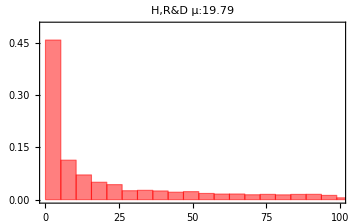
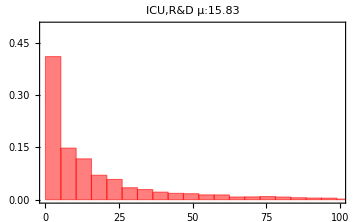
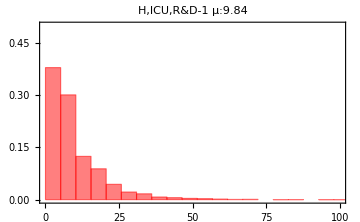
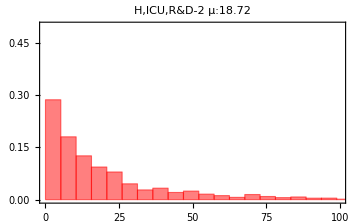
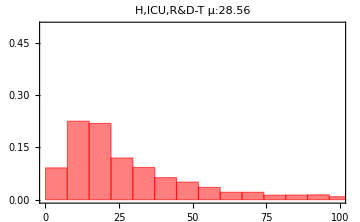
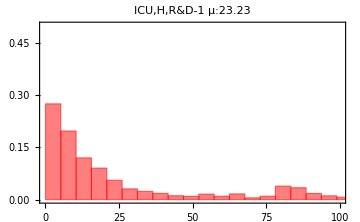
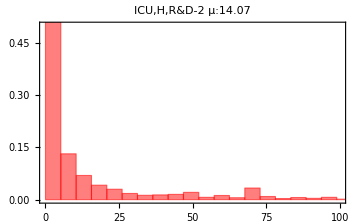
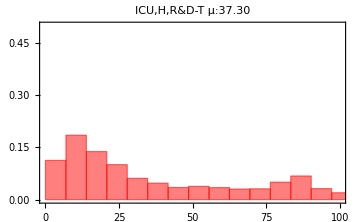

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBPH[[2;;,11]],"H,R&D μ:"},{dataBPICU[[2;;,15]],"ICU,R&D μ:"},{dataBPHICU[[2;;,11]],"H,ICU,R&D-1 μ:"},{dataBPHICU[[2;;,15]],"H,ICU,R&D-2 μ:"},{Total/@dataBPHICU[[2;;,{11,15}]],"H,ICU,R&D-T μ:"},{dataBPICUH[[2;;,15]],"ICU,H,R&D-1 μ:"},{dataBPICUH[[2;;,11]],"ICU,H,R&D-2 μ:"},{Total/@dataBPICUH[[2;;,{11,15}]],"ICU,H,R&D-T μ:"},{dataBPHICUH[[2;;,11]],"H,ICU,H,R&D-1 μ:"},{dataBPHICUH[[2;;,15]],"H,ICU,H,R&D-2 μ:"},{dataBPHICUH[[2;;,19]],"H,ICU,H,R&D-3 μ:"},{Total/@dataBPHICUH[[2;;,{11,15,19}]],"H,ICU,H,R&D-T μ:"},{dataBPICUHICU[[2;;,15]],"ICU,H,ICU,R&D-1 μ:"},{dataBPICUHICU[[2;;,11]],"ICU,H,ICU,R&D-2 μ:"},{dataBPICUHICU[[2;;,23]],"ICU,H,ICU,R&D-3 μ:"},{Total/@dataBPICUHICU[[2;;,{11,15,23}]],"ICU,H,ICU,R&D-T μ:"}}
```

```mathematica
Table[Export["/home/lina/Documents/UnCover/uncoverP1LoS/plot"<>ToString[i]<>".png",histo[[i]]],{i,Length[histo]}]
```

{/home/lina/Documents/UnCover/uncoverP1LoS/plot1.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot2.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot3.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot4.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot5.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot6.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot7.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot8.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot9.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot10.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot11.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot12.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot13.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot14.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot15.png,/home/lina/Documents/UnCover/uncoverP1LoS/plot16.png}

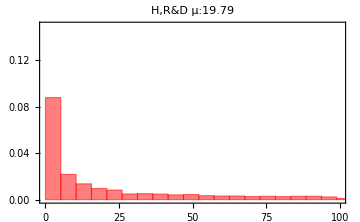
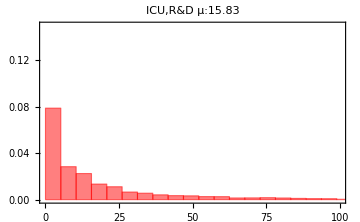
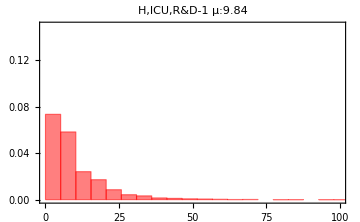
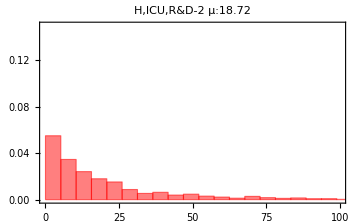
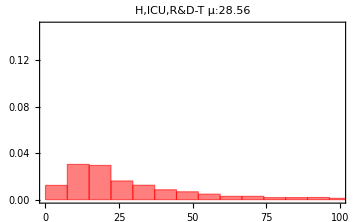
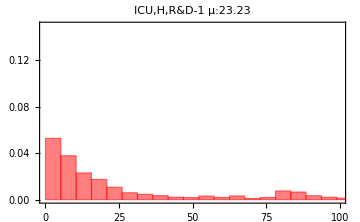
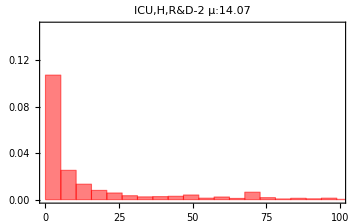
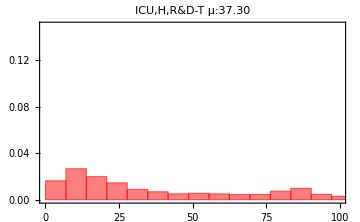

```mathematica
Apply[plotH2[#1,#2]&]/@{{dataBPH[[2;;,11]],"H,R&D μ:"},{dataBPICU[[2;;,15]],"ICU,R&D μ:"},{dataBPHICU[[2;;,11]],"H,ICU,R&D-1 μ:"},{dataBPHICU[[2;;,15]],"H,ICU,R&D-2 μ:"},{Total/@dataBPHICU[[2;;,{11,15}]],"H,ICU,R&D-T μ:"},{dataBPICUH[[2;;,15]],"ICU,H,R&D-1 μ:"},{dataBPICUH[[2;;,11]],"ICU,H,R&D-2 μ:"},{Total/@dataBPICUH[[2;;,{11,15}]],"ICU,H,R&D-T μ:"},{dataBPHICUH[[2;;,11]],"H,ICU,H,R&D-1 μ:"},{dataBPHICUH[[2;;,15]],"H,ICU,H,R&D-2 μ:"},{dataBPHICUH[[2;;,19]],"H,ICU,H,R&D-3 μ:"},{Total/@dataBPHICUH[[2;;,{11,15,19}]],"H,ICU,H,R&D-T μ:"},{dataBPICUHICU[[2;;,15]],"ICU,H,ICU,R&D-1 μ:"},{dataBPICUHICU[[2;;,11]],"ICU,H,ICU,R&D-2 μ:"},{dataBPICUHICU[[2;;,23]],"ICU,H,ICU,R&D-3 μ:"},{Total/@dataBPICUHICU[[2;;,{11,15,23}]],"ICU,H,ICU,R&D-T μ:"}}
```

### Mean by Stage and R

```mathematica
(*********************************ESTIMATING THE MEAN OF TIMES BY STAGE *)
```

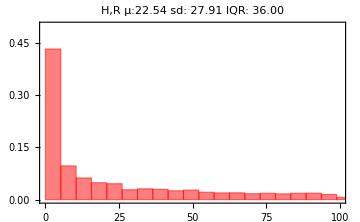
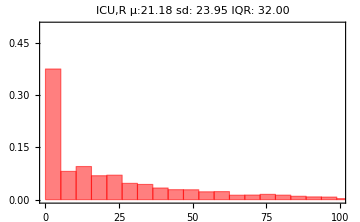
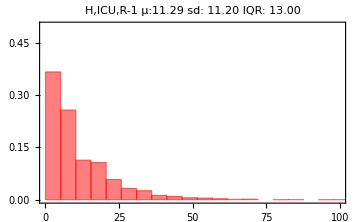
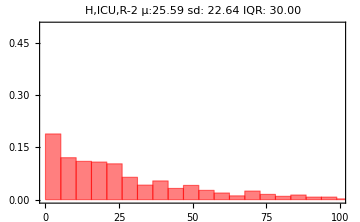
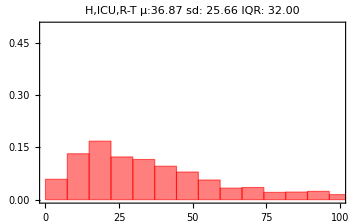
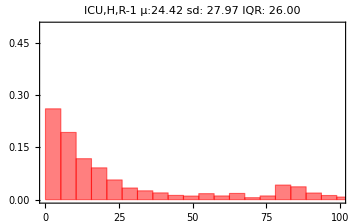
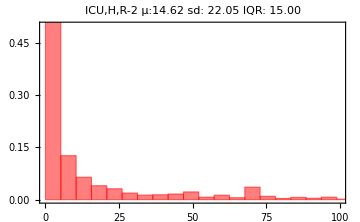
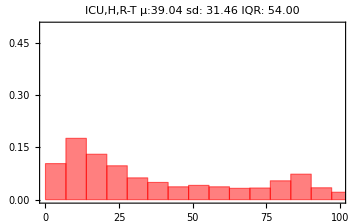

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP1[[2;;,11]],"H,R μ:"},{dataBP3[[2;;,15]],"ICU,R μ:"},{dataBP5[[2;;,11]],"H,ICU,R-1 μ:"},{dataBP5[[2;;,15]],"H,ICU,R-2 μ:"},{Total/@dataBP5[[2;;,{11,15}]],"H,ICU,R-T μ:"},{dataBP6[[2;;,15]],"ICU,H,R-1 μ:"},{dataBP6[[2;;,11]],"ICU,H,R-2 μ:"},{Total/@dataBP6[[2;;,{11,15}]],"ICU,H,R-T μ:"},{dataBP8[[2;;,11]],"H,ICU,H,R-1 μ:"},{dataBP8[[2;;,15]],"H,ICU,H,R-2 μ:"},{dataBP8[[2;;,19]],"H,ICU,H,R-3 μ:"},{Total/@dataBP8[[2;;,{11,15,19}]],"H,ICU,H,R-T μ:"},{dataBP9[[2;;,15]],"ICU,H,ICU,R-1 μ:"},{dataBP9[[2;;,11]],"ICU,H,ICU,R-2 μ:"},{dataBP9[[2;;,23]],"ICU,H,ICU,R-3 μ:"},{Total/@dataBP9[[2;;,{11,15,23}]],"ICU,H,ICU,R-T μ:"}}
```

### Mean by Stage and D

```mathematica
(*********************************ESTIMATING THE MEAN OF TIMES BY STAGE *)
```

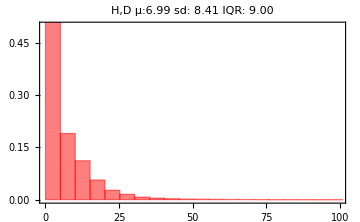
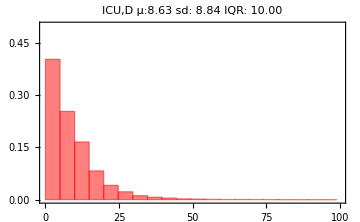
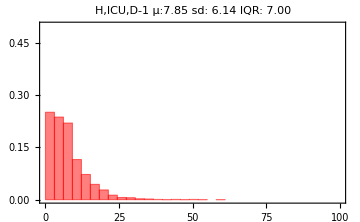
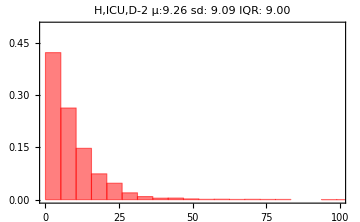
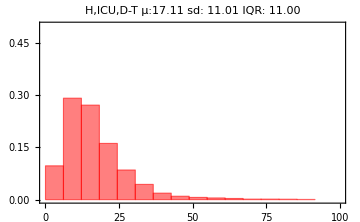
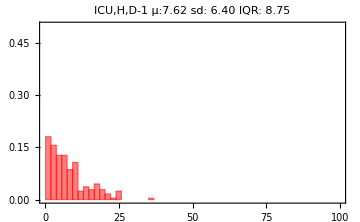
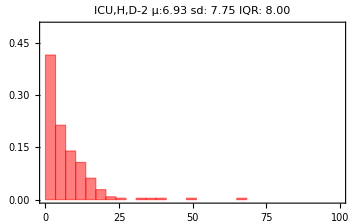
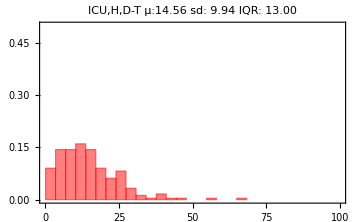

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP2[[2;;,11]],"H,D μ:"},{dataBP4[[2;;,15]],"ICU,D μ:"},{dataBP7[[2;;,11]],"H,ICU,D-1 μ:"},{dataBP7[[2;;,15]],"H,ICU,D-2 μ:"},{Total/@dataBP7[[2;;,{11,15}]],"H,ICU,D-T μ:"},{dataBP10[[2;;,15]],"ICU,H,D-1 μ:"},{dataBP10[[2;;,11]],"ICU,H,D-2 μ:"},{Total/@dataBP10[[2;;,{11,15}]],"ICU,H,D-T μ:"},{dataBP11[[2;;,11]],"H,ICU,H,D-1 μ:"},{dataBP11[[2;;,15]],"H,ICU,H,D-2 μ:"},{dataBP11[[2;;,19]],"H,ICU,H,D-3 μ:"},{Total/@dataBP11[[2;;,{11,15,19}]],"H,ICU,H,D-T μ:"},{dataBP12[[2;;,15]],"ICU,H,ICU,D-1 μ:"},{dataBP12[[2;;,11]],"ICU,H,ICU,D-2 μ:"},{dataBP12[[2;;,23]],"ICU,H,ICU,D-3 μ:"},{Total/@dataBP12[[2;;,{11,15,23}]],"ICU,H,ICU,D-T μ:"}}
```

### Mean by AGE

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP1[[2;;,11]],"H,R μ:"},{dataBP3[[2;;,15]],"ICU,R μ:"},{dataBP5[[2;;,11]],"H,ICU,R-1 μ:"},{dataBP5[[2;;,15]],"H,ICU,R-2 μ:"},{Total/@dataBP5[[2;;,{11,15}]],"H,ICU,R-T μ:"},{dataBP6[[2;;,15]],"ICU,H,R-1 μ:"},{dataBP6[[2;;,11]],"ICU,H,R-2 μ:"},{Total/@dataBP6[[2;;,{11,15}]],"ICU,H,R-T μ:"},{dataBP8[[2;;,11]],"H,ICU,H,R-1 μ:"},{dataBP8[[2;;,15]],"H,ICU,H,R-2 μ:"},{dataBP8[[2;;,19]],"H,ICU,H,R-3 μ:"},{Total/@dataBP8[[2;;,{11,15,19}]],"H,ICU,H,R-T μ:"},{dataBP9[[2;;,15]],"ICU,H,ICU,R-1 μ:"},{dataBP9[[2;;,11]],"ICU,H,ICU,R-2 μ:"},{dataBP9[[2;;,23]],"ICU,H,ICU,R-3 μ:"},{Total/@dataBP9[[2;;,{11,15,23}]],"ICU,H,ICU,R-T μ:"}}
```

```mathematica
data7[[2;;,3]]//Tally//Sort
```

{{1_25,22310},{26_50,78960},{51_65,68366},{66_75,38794},{75_,34253},{NA,2688}}

```mathematica
dataBP5=Select[Select[data7,#[[9]]==5&],#[[11]]!="NA"&&#[[15]]!="NA"&];(*HICUR*)
dataBP7=Select[Select[data7,#[[9]]==7&],#[[11]]!="NA"&&#[[15]]!="NA"&];(*HICUD*)
dataBP6=Select[Select[data7,#[[9]]==6&],#[[11]]!="NA"&&#[[15]]!="NA"&];(*ICUHR*)
dataBP10=Select[Select[data7,#[[9]]==10&],#[[11]]!="NA"&&#[[15]]!="NA"&];(*ICUHD*)
```

#### HR

```mathematica
dataBP1g1=Select[data7,#[[9]]==1&&#[[11]]!="NA"&&#[[3]]=="1_25"&][[1;;,11]];(*HR*)
dataBP1g2=Select[data7,#[[9]]==1&&#[[11]]!="NA"&&#[[3]]=="26_50"&][[1;;,11]];(*HR*)
dataBP1g3=Select[data7,#[[9]]==1&&#[[11]]!="NA"&&#[[3]]=="51_65"&][[1;;,11]];(*HR*)
dataBP1g4=Select[data7,#[[9]]==1&&#[[11]]!="NA"&&#[[3]]=="66_75"&][[1;;,11]];(*HR*)
dataBP1g5=Select[data7,#[[9]]==1&&#[[11]]!="NA"&&#[[3]]=="75_"&][[1;;,11]];(*HR*)
```

```mathematica
dataBP1[[2;;,3]]//Tally//Sort
```

{{1_25,18629},{26_50,58832},{51_65,40267},{66_75,18418},{75_,13924},{NA,2010}}

```mathematica
Length/@{dataBP1g1,dataBP1g2,dataBP1g3,dataBP1g4,dataBP1g5}
```

{18629,58833,40267,18418,13924}

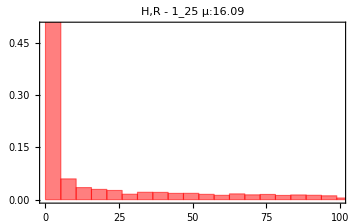
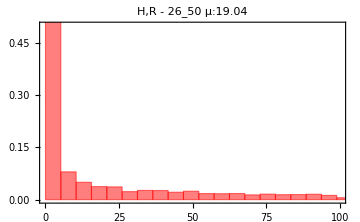
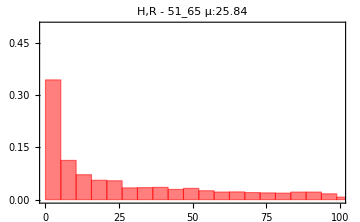
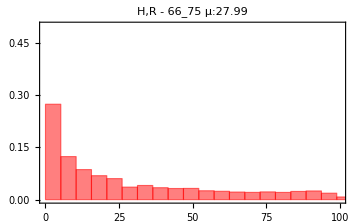
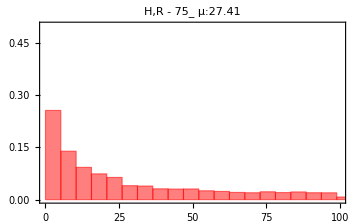

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP1g1,"H,R - 1_25 μ:"},{dataBP1g2,"H,R - 26_50 μ:"},{dataBP1g3,"H,R - 51_65 μ:"},{dataBP1g4,"H,R - 66_75 μ:"},{dataBP1g5,"H,R - 75_ μ:"}}
```

#### HD

```mathematica
dataBP2g1=Select[data7,#[[9]]==2&&#[[11]]!="NA"&&#[[3]]=="1_25"&][[1;;,11]];(*HD*)
dataBP2g2=Select[data7,#[[9]]==2&&#[[11]]!="NA"&&#[[3]]=="26_50"&][[1;;,11]];(*HD*)
dataBP2g3=Select[data7,#[[9]]==2&&#[[11]]!="NA"&&#[[3]]=="51_65"&][[1;;,11]];(*HD*)
dataBP2g4=Select[data7,#[[9]]==2&&#[[11]]!="NA"&&#[[3]]=="66_75"&][[1;;,11]];(*HD*)
dataBP2g5=Select[data7,#[[9]]==2&&#[[11]]!="NA"&&#[[3]]=="75_"&][[1;;,11]];(*HD*)
```

```mathematica
dataBP2[[2;;,3]]//Tally//Sort
```

{{1_25,287},{26_50,3485},{51_65,8123},{66_75,8397},{75_,12386},{NA,26}}

```mathematica
Length/@{dataBP2g1,dataBP2g2,dataBP2g3,dataBP2g4,dataBP2g5}
```

{287,3485,8123,8397,12387}

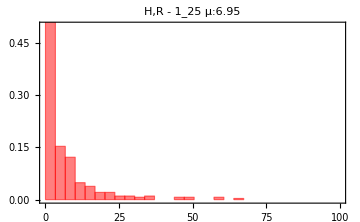
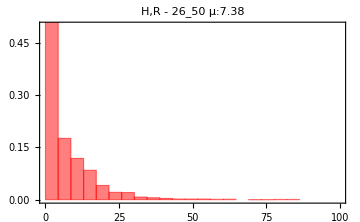
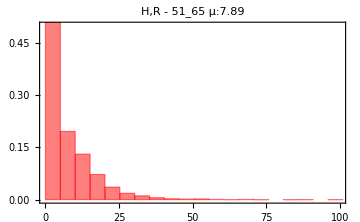
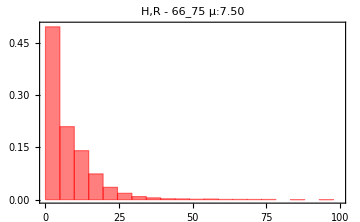
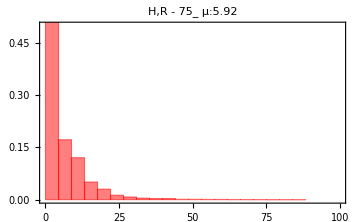

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP2g1,"H,R - 1_25 μ:"},{dataBP2g2,"H,R - 26_50 μ:"},{dataBP2g3,"H,R - 51_65 μ:"},{dataBP2g4,"H,R - 66_75 μ:"},{dataBP2g5,"H,R - 75_ μ:"}}
```

#### ICUR

```mathematica
dataBP3g1=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="1_25"&][[All,15]];(*ICUR*)
dataBP3g2=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="26_50"&][[All,15]];(*ICUR*)
dataBP3g3=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="51_65"&][[All,15]];(*ICUR*)
dataBP3g4=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="66_75"&][[All,15]];(*ICUR*)
dataBP3g5=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="75_"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP3[[2;;,3]]//Tally//Sort
```

{{1_25,1547},{26_50,6923},{51_65,5788},{66_75,2293},{75_,1088},{NA,187}}

```mathematica
Length/@{dataBP3g1,dataBP3g2,dataBP3g3,dataBP3g4,dataBP3g5}
```

{1547,6923,5789,2293,1088}

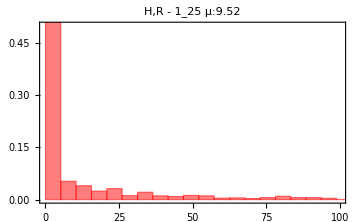
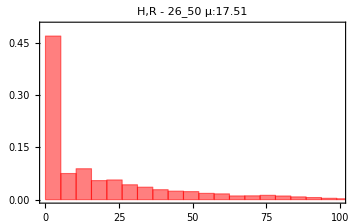
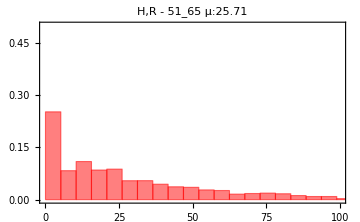
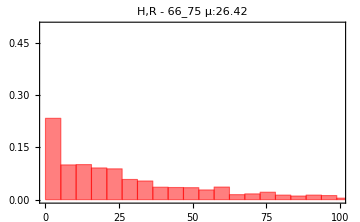
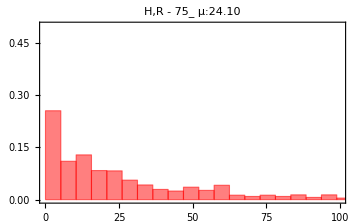

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP3g1,"H,R - 1_25 μ:"},{dataBP3g2,"H,R - 26_50 μ:"},{dataBP3g3,"H,R - 51_65 μ:"},{dataBP3g4,"H,R - 66_75 μ:"},{dataBP3g5,"H,R - 75_ μ:"}}
```

#### ICUD

```mathematica
dataBP4g1=Select[data7,#[[9]]==4&&#[[15]]!="NA"&&#[[3]]=="1_25"&][[All,15]];(*ICUR*)
dataBP4g2=Select[data7,#[[9]]==4&&#[[15]]!="NA"&&#[[3]]=="26_50"&][[All,15]];(*ICUR*)
dataBP4g3=Select[data7,#[[9]]==4&&#[[15]]!="NA"&&#[[3]]=="51_65"&][[All,15]];(*ICUR*)
dataBP4g4=Select[data7,#[[9]]==4&&#[[15]]!="NA"&&#[[3]]=="66_75"&][[All,15]];(*ICUR*)
dataBP4g5=Select[data7,#[[9]]==4&&#[[15]]!="NA"&&#[[3]]=="75_"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP4[[2;;,3]]//Tally//Sort
```

{{1_25,99},{26_50,2010},{51_65,4527},{66_75,3702},{75_,2888},{NA,11}}

```mathematica
Length/@{dataBP4g1,dataBP4g2,dataBP4g3,dataBP4g4,dataBP4g5}
```

{99,2010,4528,3702,2888}

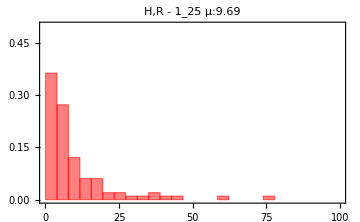
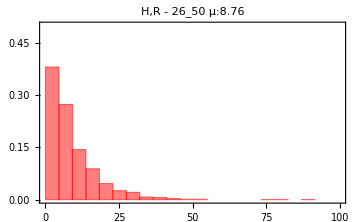
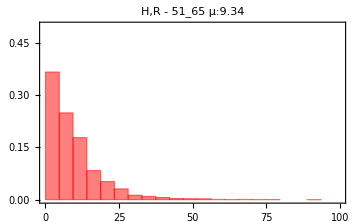
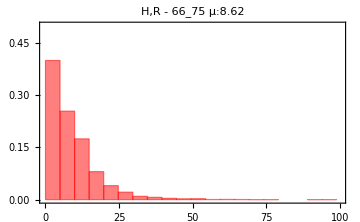
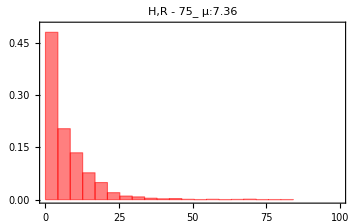

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP4g1,"H,R - 1_25 μ:"},{dataBP4g2,"H,R - 26_50 μ:"},{dataBP4g3,"H,R - 51_65 μ:"},{dataBP4g4,"H,R - 66_75 μ:"},{dataBP4g5,"H,R - 75_ μ:"}}
```

#### HICUR

```mathematica
dataBP3g1=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="1_25"&][[All,15]];(*ICUR*)
dataBP3g2=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="26_50"&][[All,15]];(*ICUR*)
dataBP3g3=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="51_65"&][[All,15]];(*ICUR*)
dataBP3g4=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="66_75"&][[All,15]];(*ICUR*)
dataBP3g5=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="75_"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP3[[2;;,3]]//Tally//Sort
```

{{1_25,1547},{26_50,6923},{51_65,5788},{66_75,2293},{75_,1088},{NA,187}}

```mathematica
Length/@{dataBP3g1,dataBP3g2,dataBP3g3,dataBP3g4,dataBP3g5}
```

{1547,6923,5789,2293,1088}

#### HICUD

```mathematica
dataBP3g1=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="1_25"&][[All,15]];(*ICUR*)
dataBP3g2=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="26_50"&][[All,15]];(*ICUR*)
dataBP3g3=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="51_65"&][[All,15]];(*ICUR*)
dataBP3g4=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="66_75"&][[All,15]];(*ICUR*)
dataBP3g5=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="75_"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP3[[2;;,3]]//Tally//Sort
```

{{1_25,1547},{26_50,6923},{51_65,5788},{66_75,2293},{75_,1088},{NA,187}}

```mathematica
Length/@{dataBP3g1,dataBP3g2,dataBP3g3,dataBP3g4,dataBP3g5}
```

{1547,6923,5789,2293,1088}

#### ICUHR

```mathematica
dataBP3g1=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="1_25"&][[All,15]];(*ICUR*)
dataBP3g2=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="26_50"&][[All,15]];(*ICUR*)
dataBP3g3=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="51_65"&][[All,15]];(*ICUR*)
dataBP3g4=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="66_75"&][[All,15]];(*ICUR*)
dataBP3g5=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="75_"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP3[[2;;,3]]//Tally//Sort
```

{{1_25,1547},{26_50,6923},{51_65,5788},{66_75,2293},{75_,1088},{NA,187}}

```mathematica
Length/@{dataBP3g1,dataBP3g2,dataBP3g3,dataBP3g4,dataBP3g5}
```

{1547,6923,5789,2293,1088}

#### ICUHD

```mathematica
dataBP3g1=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="1_25"&][[All,15]];(*ICUR*)
dataBP3g2=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="26_50"&][[All,15]];(*ICUR*)
dataBP3g3=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="51_65"&][[All,15]];(*ICUR*)
dataBP3g4=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="66_75"&][[All,15]];(*ICUR*)
dataBP3g5=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="75_"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP3[[2;;,3]]//Tally//Sort
```

{{1_25,1547},{26_50,6923},{51_65,5788},{66_75,2293},{75_,1088},{NA,187}}

```mathematica
Length/@{dataBP3g1,dataBP3g2,dataBP3g3,dataBP3g4,dataBP3g5}
```

{1547,6923,5789,2293,1088}

### Mean by GENDER

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP1[[2;;,11]],"H,R μ:"},{dataBP3[[2;;,15]],"ICU,R μ:"},{dataBP5[[2;;,11]],"H,ICU,R-1 μ:"},{dataBP5[[2;;,15]],"H,ICU,R-2 μ:"},{Total/@dataBP5[[2;;,{11,15}]],"H,ICU,R-T μ:"},{dataBP6[[2;;,15]],"ICU,H,R-1 μ:"},{dataBP6[[2;;,11]],"ICU,H,R-2 μ:"},{Total/@dataBP6[[2;;,{11,15}]],"ICU,H,R-T μ:"},{dataBP8[[2;;,11]],"H,ICU,H,R-1 μ:"},{dataBP8[[2;;,15]],"H,ICU,H,R-2 μ:"},{dataBP8[[2;;,19]],"H,ICU,H,R-3 μ:"},{Total/@dataBP8[[2;;,{11,15,19}]],"H,ICU,H,R-T μ:"},{dataBP9[[2;;,15]],"ICU,H,ICU,R-1 μ:"},{dataBP9[[2;;,11]],"ICU,H,ICU,R-2 μ:"},{dataBP9[[2;;,23]],"ICU,H,ICU,R-3 μ:"},{Total/@dataBP9[[2;;,{11,15,23}]],"ICU,H,ICU,R-T μ:"}}
```

```mathematica
data7[[2;;,4]]//Tally//Sort
```

{{F,109006},{M,136365}}

```mathematica
dataBP5=Select[Select[data7,#[[9]]==5&],#[[11]]!="NA"&&#[[15]]!="NA"&];(*HICUR*)
dataBP7=Select[Select[data7,#[[9]]==7&],#[[11]]!="NA"&&#[[15]]!="NA"&];(*HICUD*)
dataBP6=Select[Select[data7,#[[9]]==6&],#[[11]]!="NA"&&#[[15]]!="NA"&];(*ICUHR*)
dataBP10=Select[Select[data7,#[[9]]==10&],#[[11]]!="NA"&&#[[15]]!="NA"&];(*ICUHD*)
```

#### HR

```mathematica
dataBP1gM=Select[data7,#[[9]]==1&&#[[11]]!="NA"&&#[[4]]=="M"&][[1;;,11]];(*HR*)
dataBP1gF=Select[data7,#[[9]]==1&&#[[11]]!="NA"&&#[[4]]=="F"&][[1;;,11]];(*HR*)
```

```mathematica
dataBP1[[2;;,4]]//Tally//Sort
```

{{F,71552},{M,80528}}

```mathematica
Length/@{dataBP1gM,dataBP1gF}
```

{80529,71552}

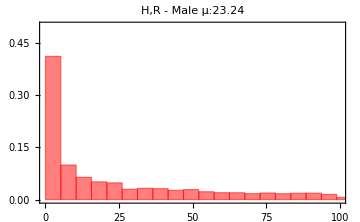
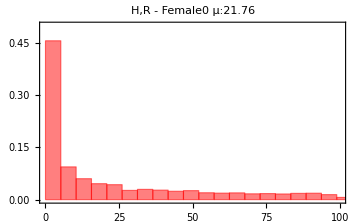

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP1gM,"H,R - Male μ:"},{dataBP1gF,"H,R - Female0 μ:"}}
```

#### HD

```mathematica
dataBP2gM=Select[data7,#[[9]]==2&&#[[11]]!="NA"&&#[[4]]=="M"&][[1;;,11]];(*HD*)
dataBP2gF=Select[data7,#[[9]]==2&&#[[11]]!="NA"&&#[[4]]=="F"&][[1;;,11]];(*HD*)
```

```mathematica
dataBP2[[2;;,4]]//Tally//Sort
```

{{F,12833},{M,19871}}

```mathematica
Length/@{dataBP2gM,dataBP2gF}
```

{19872,12833}

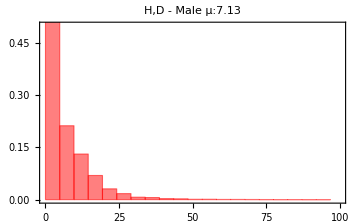
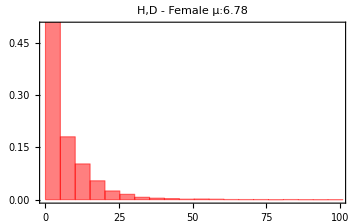

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP2gM,"H,D - Male μ:"},{dataBP2gF,"H,D - Female μ:"}}
```

#### ICUR

```mathematica
dataBP3gM=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[4]]=="M"&][[All,15]];(*ICUR*)
dataBP3gF=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[4]]=="F"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP3[[2;;,4]]//Tally//Sort
```

{{F,7567},{M,10259}}

```mathematica
Length/@{dataBP3gM,dataBP3gF}
```

{10259,7568}

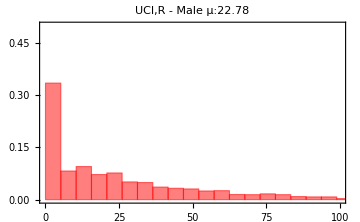
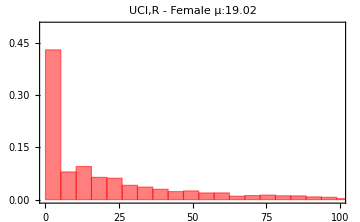

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP3gM,"UCI,R - Male μ:"},{dataBP3gF,"UCI,R - Female μ:"}}
```

#### ICUD

```mathematica
dataBP4gM=Select[data7,#[[9]]==4&&#[[15]]!="NA"&&#[[4]]=="M"&][[All,15]];(*ICUR*)
dataBP4gF=Select[data7,#[[9]]==4&&#[[15]]!="NA"&&#[[4]]=="F"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP4[[2;;,4]]//Tally//Sort
```

{{F,4881},{M,8356}}

```mathematica
Length/@{dataBP4gM,dataBP4gF}
```

{8357,4881}

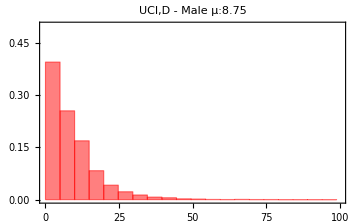
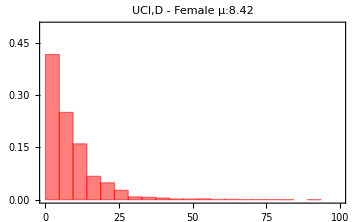

```mathematica
histo=Apply[plotH[#1,#2]&]/@{{dataBP4gM,"UCI,D - Male μ:"},{dataBP4gF,"UCI,D - Female μ:"}}
```

#### HICUR

```mathematica
dataBP3g1=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="1_25"&][[All,15]];(*ICUR*)
dataBP3g2=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="26_50"&][[All,15]];(*ICUR*)
dataBP3g3=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="51_65"&][[All,15]];(*ICUR*)
dataBP3g4=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="66_75"&][[All,15]];(*ICUR*)
dataBP3g5=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="75_"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP3[[2;;,3]]//Tally//Sort
```

{{1_25,1547},{26_50,6923},{51_65,5788},{66_75,2293},{75_,1088},{NA,187}}

```mathematica
Length/@{dataBP3g1,dataBP3g2,dataBP3g3,dataBP3g4,dataBP3g5}
```

{1547,6923,5789,2293,1088}

#### HICUD

```mathematica
dataBP3g1=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="1_25"&][[All,15]];(*ICUR*)
dataBP3g2=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="26_50"&][[All,15]];(*ICUR*)
dataBP3g3=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="51_65"&][[All,15]];(*ICUR*)
dataBP3g4=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="66_75"&][[All,15]];(*ICUR*)
dataBP3g5=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="75_"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP3[[2;;,3]]//Tally//Sort
```

{{1_25,1547},{26_50,6923},{51_65,5788},{66_75,2293},{75_,1088},{NA,187}}

```mathematica
Length/@{dataBP3g1,dataBP3g2,dataBP3g3,dataBP3g4,dataBP3g5}
```

{1547,6923,5789,2293,1088}

#### ICUHR

```mathematica
dataBP3g1=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="1_25"&][[All,15]];(*ICUR*)
dataBP3g2=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="26_50"&][[All,15]];(*ICUR*)
dataBP3g3=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="51_65"&][[All,15]];(*ICUR*)
dataBP3g4=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="66_75"&][[All,15]];(*ICUR*)
dataBP3g5=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="75_"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP3[[2;;,3]]//Tally//Sort
```

{{1_25,1547},{26_50,6923},{51_65,5788},{66_75,2293},{75_,1088},{NA,187}}

```mathematica
Length/@{dataBP3g1,dataBP3g2,dataBP3g3,dataBP3g4,dataBP3g5}
```

{1547,6923,5789,2293,1088}

#### ICUHD

```mathematica
dataBP3g1=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="1_25"&][[All,15]];(*ICUR*)
dataBP3g2=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="26_50"&][[All,15]];(*ICUR*)
dataBP3g3=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="51_65"&][[All,15]];(*ICUR*)
dataBP3g4=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="66_75"&][[All,15]];(*ICUR*)
dataBP3g5=Select[data7,#[[9]]==3&&#[[15]]!="NA"&&#[[3]]=="75_"&][[All,15]];(*ICUR*)
```

```mathematica
dataBP3[[2;;,3]]//Tally//Sort
```

{{1_25,1547},{26_50,6923},{51_65,5788},{66_75,2293},{75_,1088},{NA,187}}

```mathematica
Length/@{dataBP3g1,dataBP3g2,dataBP3g3,dataBP3g4,dataBP3g5}
```

{1547,6923,5789,2293,1088}

## Estimations from the AFTf results

### Functions

```mathematica
f[dis_]:=Plot[PDF[dis,x],{x,0,100},PlotRange->All, PlotLabel->"Mean: "<>ToString[Mean[dis]]<>" Sd: "<>ToString[StandardDeviation[dis]]<>"\n Median: "<>ToString[Median[dis]]<>" IQR: "<>ToString[InterquartileRange[dis]]<>" Mode: "<>ToString[Commonest[IntegerPart [#]&/@RandomVariate[dis,1000]]],ImageSize->Medium]
```

### For the whole data outcome R&D

#### H - RD

without adjustment

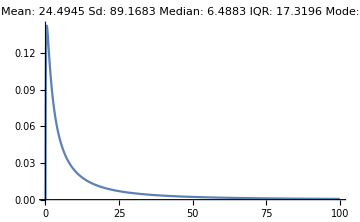
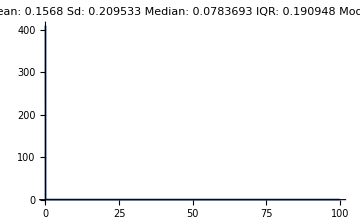
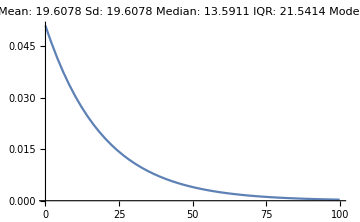
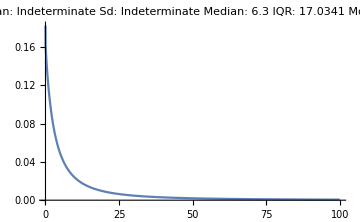
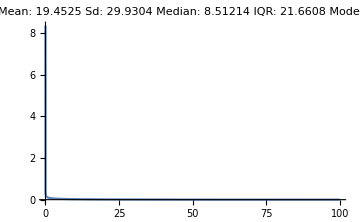

```mathematica
f[#]&/@{LogNormalDistribution[1.87,1.63],GammaDistribution[0.56,0.28],ExponentialDistribution[0.051],LogLogisticDistribution[0.99,6.30],WeibullDistribution[0.67,14.71]}
```

adjusted by gender

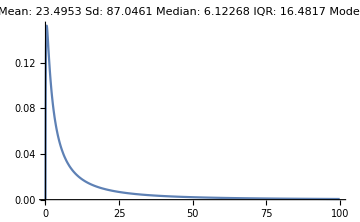

```mathematica
f[#]&/@{LogNormalDistribution[1.812,1.64]}
```

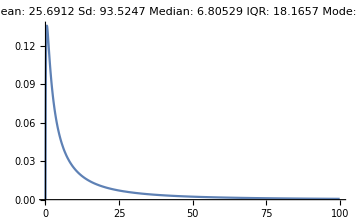

```mathematica
f[#]&/@{LogNormalDistribution[1.812+0.1057,1.63]}
```

```mathematica
25.69/23.49
```

1.09366

```mathematica
6.805/6.123
```

1.11138

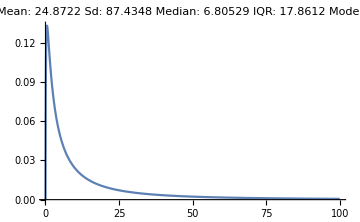

```mathematica
f[#]&/@{LogNormalDistribution[1.812+0.1057,1.63-0.020]}
```

```mathematica
24.8722/23.4953
```

1.0586

```mathematica
87.4348/87.0461
```

1.00447

```mathematica
(1.81207+0.10568)/1.81207
```

1.05832

```mathematica
(1.64553-0.02003)/1.64553
```

0.987828

```mathematica
(*CONLUSION: The correct form to get the distribution for the comparison group is to sum the "est" of comparison group to the location parameter of base group. In this way I get the exp(est) with the ratio of parameters btween both distributions*)
```

adjusted by age

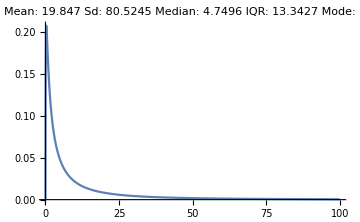

```mathematica
f[#]&/@{LogNormalDistribution[1.55806,1.69115]}
```

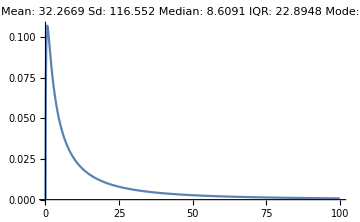

```mathematica
f[#]&/@{LogNormalDistribution[1.55806+0.59476,1.69115-0.06559]}
```

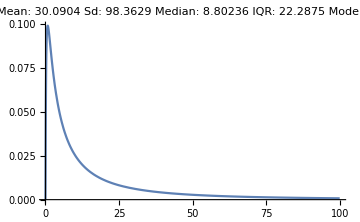

```mathematica
f[#]&/@{LogNormalDistribution[1.55806+.61696,1.69115-0.12323]}
```

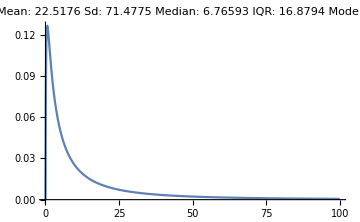

```mathematica
f[#]&/@{LogNormalDistribution[1.55806+0.35384,1.69115-0.14041]}
```

adjusted by Wave with the first wave as basal group

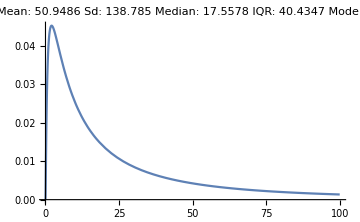

```mathematica
f[#]&/@{LogNormalDistribution[2.86550,1.45967]} (*w1*)
```

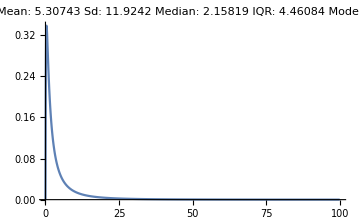

```mathematica
f[#]&/@{LogNormalDistribution[2.86550-2.09623,1.45967-0.11815]}(*w2*)
```

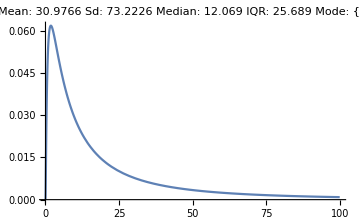

```mathematica
f[#]&/@{LogNormalDistribution[2.86550-0.37486,1.45967-0.08665]}(*w3*)
```

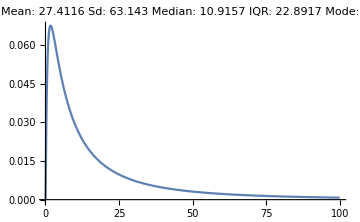

```mathematica
f[#]&/@{LogNormalDistribution[2.86550-0.47530,1.45967-0.10264]}(*w4*)
```

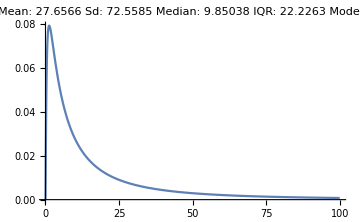

```mathematica
f[#]&/@{LogNormalDistribution[2.86550-0.57799,1.45967-0.02276]}(*w5*)
```

adjusted by Wave with the second wave as basal group

```mathematica
f[#]&/@{LogNormalDistribution[0.76919,1.29713]}(*w2*)
```

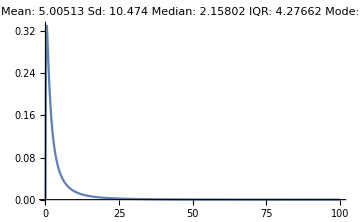

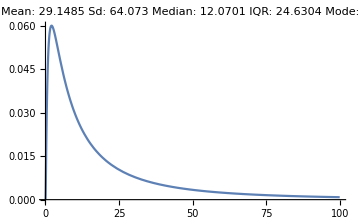

```mathematica
f[#]&/@{LogNormalDistribution[0.76919+1.72154,1.29713+0.03078]}(*w3*)
```

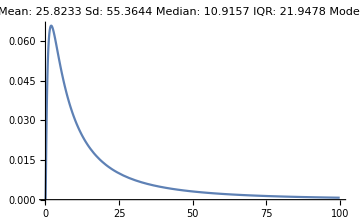

```mathematica
f[#]&/@{LogNormalDistribution[0.76919+1.62101,1.29713+0.01518]}(*w4*)
```

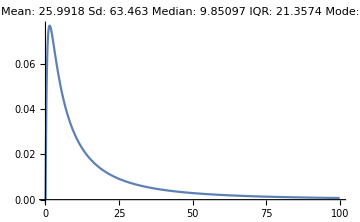

```mathematica
f[#]&/@{LogNormalDistribution[0.76919+1.51838,1.29713+0.09586]}(*w5*)
```

adjusted by Wave with the second wave as basal group

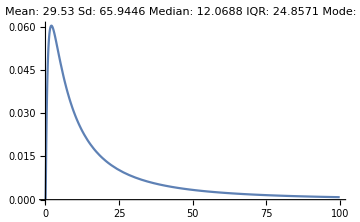

```mathematica
f[#]&/@{LogNormalDistribution[2.49062,1.33775]}(*w3*)
```

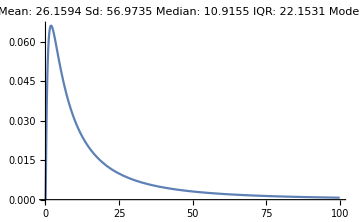

```mathematica
f[#]&/@{LogNormalDistribution[2.49062-0.10044,1.33775-0.01561]}(*w4*)
```

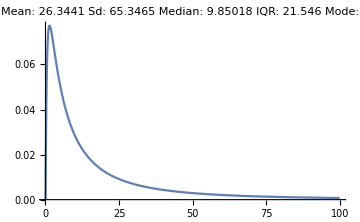

```mathematica
f[#]&/@{LogNormalDistribution[2.49062-0.20313,1.33775+0.06493]}(*w5*)
```

CONCLUTION:  It does not matter who is the basal group the time distribution built for each category is almost the same although the estimates change according to the model-basal group

adjusted by PeaksValleys

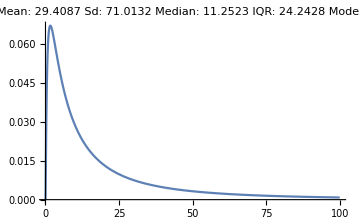

```mathematica
f[#]&/@{LogNormalDistribution[2.42057,1.38616]}(*peaks*)
```

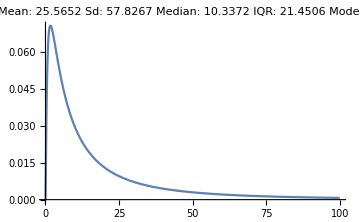

```mathematica
f[#]&/@{LogNormalDistribution[2.42057-0.08482,1.38616-0.04044]}(*valley*)
```

#### H-ICUf

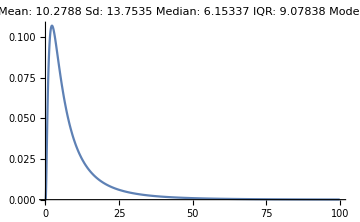

```mathematica
f[#]&/@{LogNormalDistribution[1.817,1.013]}
```

gender

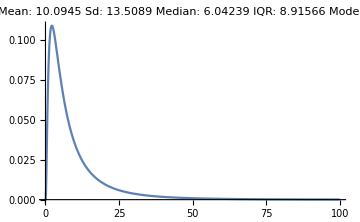

```mathematica
f[#]&/@{LogNormalDistribution[1.7988,1.0131]}
```

```mathematica
(*Gender did not change significantly the parameters *)
```

adjusted by age

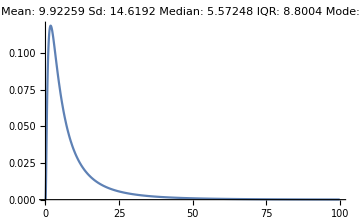

```mathematica
f[#]&/@{LogNormalDistribution[1.71784,1.07422]}
```

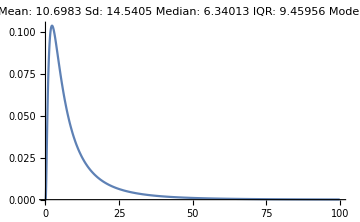

```mathematica
f[#]&/@{LogNormalDistribution[1.71784+0.12906,1.07422-0.05130]}
```

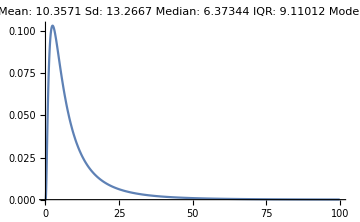

```mathematica
f[#]&/@{LogNormalDistribution[1.71784+0.13430,1.07422-0.08879]}
```

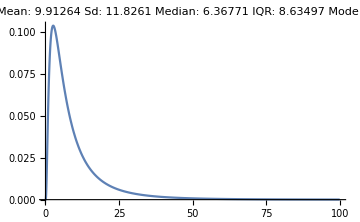

```mathematica
f[#]&/@{LogNormalDistribution[1.71784+0.13340,1.07422-0.13340]}
```

adjusted by Wave with the first wave as basal group

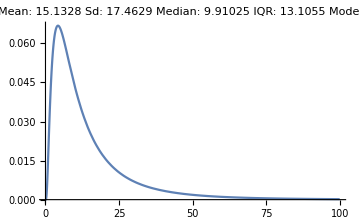

```mathematica
f[#]&/@{LogNormalDistribution[2.29357,0.92010]}
```

```mathematica
f[#]&/@{LogNormalDistribution[2.29357-0.51514,0.92010+0.03407]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[2.29357-0.43773,0.920100+.04820]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[2.29357-0.88003,0.92010+0.03786]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[2.29357-0.81815,0.920100+.12897]}
```

{-Graphics-}

```mathematica
(*Gamma es la distribucion con menor AIC. puse las anteriores para comparar porque los est y exp(est) son muy diferentes*)
```

```mathematica
f[#]&/@{GammaDistribution[1.61098,0.115541]}
```

{-Graphics-}

```mathematica
(*LAS FUNCIONES GAMMA NO SON UNA BUENA OPCIÓN*)
```

#### ICUf-RD

```mathematica
f[#]&/@{LogNormalDistribution[1.901,1.427]}
```

{-Graphics-}

gender

```mathematica
f[#]&/@{LogNormalDistribution[1.78364,1.42357]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.78364+0.19668,1.42357]}
```

{-Graphics-}

```mathematica
1.78364+0.19668/1.78364
```

1.89391

```mathematica
19.96/16.39
```

1.21782

```mathematica
(**cuando se estima el cambio en sdlog tambien, los parametros basales también cambian*)
```

```mathematica
f[#]&/@{LogNormalDistribution[1.78364,1.44902]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.78364+0.19668,1.44902-0.02993]}
```

{-Graphics-}

```mathematica
19.83/16.39
```

1.20988

```mathematica
45.511/50.527
```

0.900726

```mathematica
1.78364+0.19668/1.78364
```

1.89391

```mathematica
1.44902/1.44902-0.02993
```

0.97007

adjusted by age

```mathematica
f[#]&/@{LogNormalDistribution[1.61598,1.54474]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.61598+0.57114,1.54474-0.12718]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.61598+0.41804,1.54474-0.17165]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.61598+0.12011,1.54474-0.19257]}
```

{-Graphics-}

#### H-ICUf-RD

```mathematica
f[#]&/@{LogNormalDistribution[3.023,0.779]}
```

{-Graphics-}

gender no significative

adjusted by age

```mathematica
f[#]&/@{LogNormalDistribution[3.07757,0.83117]}
```

{-Graphics-}

```mathematica
(*G2 no es significativo*)
```

```mathematica
f[#]&/@{LogNormalDistribution[3.07757-0.08733,0.83117-0.10423]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[3.07757-0.17327,0.83117-0.12886]}
```

{-Graphics-}

#### H - ICUt

```mathematica
f[#]&/@{LogNormalDistribution[1.912,1.063]}
```

{-Graphics-}

gender no significative

age no significative

#### ICUt-H2

```mathematica
f[#]&/@{LogNormalDistribution[1.907,1.267]}
```

{-Graphics-}

gender no significative

age no significative

#### H2-RD

```mathematica
f[#]&/@{LogNormalDistribution[1.757,1.369]}
```

{-Graphics-}

gender no significative

age no significative

#### H - ICUt - H2 - RD

```mathematica
f[#]&/@{LogNormalDistribution[3.419,0.728]}
```

{-Graphics-}

gender no significative

age no significative

#### ICU-RD

```mathematica
f[#]&/@{LogNormalDistribution[1.901,1.427]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.78364,1.44902]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.78364+0.19667,1.44902-0.02993]}
```

{-Graphics-}

adjusted by age

```mathematica
f[#]&/@{LogNormalDistribution[1.61598,1.54474]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.61598+0.57114,1.54474-0.12718]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.61598+0.41804,1.54474-0.17165]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.61598+0.12011,1.54474-0.19257]}
```

{-Graphics-}

#### ICU-Hf

```mathematica
f[#]&/@{LogNormalDistribution[2.369,1.312]}
```

{-Graphics-}

adjusted by age

```mathematica
f[#]&/@{LogNormalDistribution[2.4121,1.3278]}
```

{-Graphics-}

```mathematica
(*G2 y G3 no significative*)
```

```mathematica
f[#]&/@{LogNormalDistribution[2.4121-0.3245,1.3278]}
```

{-Graphics-}

#### Hf-RD

```mathematica
f[#]&/@{LogNormalDistribution[1.593,1.377]}
```

{-Graphics-}

gender no significative

age no significative

#### ICU-Hf-RD

```mathematica
f[#]&/@{GammaDistribution[1.352,0.038],WeibullDistribution[1.198,37.452],LogNormalDistribution[3.147,0.986]}
```

{-Graphics-,-Graphics-,-Graphics-}

adjusted by age

```mathematica
f[#]&/@{WeibullDistribution[1.20082,39.11651]}
```

{-Graphics-}

```mathematica
(*G2 no significative*)
```

```mathematica
f[#]&/@{WeibullDistribution[1.20082-0.12886,39.11651]}
```

{-Graphics-}

```mathematica
f[#]&/@{WeibullDistribution[1.20082-0.18820,39.11651]}
```

{-Graphics-}

#### ICU-Ht

```mathematica
f[#]&/@{LogNormalDistribution[1.867,1.080]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[2.00460,1.08103]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[2.00460-0.21781,1.08103-0.00903]}
```

{-Graphics-}

age no significative

#### Ht-ICU2

```mathematica
f[#]&/@{LogNormalDistribution[0.985,0.903]}
```

{-Graphics-}

gender no significative

age no significative

#### ICU2-RD

```mathematica
f[#]&/@{LogNormalDistribution[1.851,1.240]}
```

{-Graphics-}

gender no significative

age

```mathematica
f[#]&/@{LogNormalDistribution[1.99071,1.2092]}
```

{-Graphics-}

```mathematica
(* G2 y G3 no significative*)
```

```mathematica
f[#]&/@{LogNormalDistribution[1.99071-0.4261,1.2092]}
```

{-Graphics-}

#### ICU-Ht-ICU2-RD

```mathematica
f[#]&/@{LogNormalDistribution[3.0828,0.7255]}
```

{-Graphics-}

gender no significative

age

```mathematica
f[#]&/@{LogNormalDistribution[3.18691,0.71147]}
```

{-Graphics-}

```mathematica
(*G2  no significative*)
```

```mathematica
f[#]&/@{LogNormalDistribution[3.18691-0.20407,0.71147]}
```

{-Graphics-}

```mathematica
(*G4 no significative*)
```

### For the whole data outcome R

#### H - R

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.98716,1.69306]}
```

{-Graphics-}

adjusted by gender

```mathematica
f[#]&/@{LogNormalDistribution[1.90860,1.70296]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.90860+0.14836,1.70296-0.01288]}
```

{-Graphics-}

adjusted by age

```mathematica
f[#]&/@{LogNormalDistribution[1.56842,1.71268]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.56842+0.71865,1.71268-0.05644]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.56842+0.94068,1.71268-0.12782]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.56842+0.97095,1.71268-0.16144]}
```

{-Graphics-}

#### H-ICUf

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.8817,1.0951]}
```

{-Graphics-}

no significative gender

adjusted by age

```mathematica
f[#]&/@{WeibullDistribution[0.9808,19.94152]}
```

{-Graphics-}

```mathematica
f[#]&/@{WeibullDistribution[0.9808+0.1003,19.94152+0.1354]}
```

{-Graphics-}

```mathematica
f[#]&/@{WeibullDistribution[0.9808+0.1267,19.94152+0.1975]}
```

{-Graphics-}

```mathematica
f[#]&/@{WeibullDistribution[0.9808+0.1313,19.94152+0.1829]}
```

{-Graphics-}

#### ICUf-R

without adjustment

```mathematica
f[#]&/@{WeibullDistribution[0.74288,17.68741]}
```

{-Graphics-}

adjusted by gender

```mathematica
f[#]&/@{WeibullDistribution[0.69789,14.92029]}
```

{-Graphics-}

```mathematica
f[#]&/@{WeibullDistribution[0.69789+0.11832,14.92029+0.28786]}
```

{-Graphics-}

adjusted by age

```mathematica
f[#]&/@{LogNormalDistribution[1.5974,1.6450]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.5974+0.9234,1.6450-0.1190]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.5974+1.0062,1.6450-0.1536]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.5974+0.8411,1.6450-0.1424]}
```

{-Graphics-}

#### H-ICUf-R

without adjustment

```mathematica
f[#]&/@{WeibullDistribution[1.5669,38.8273]}
```

{-Graphics-}

adjusted by gender

```mathematica
f[#]&/@{WeibullDistribution[1.51875,37.65565]}
```

{-Graphics-}

```mathematica
f[#]&/@{WeibullDistribution[1.51875+0.05229,37.65565+0.04977]}
```

{-Graphics-}

adjusted by age

```mathematica
f[#]&/@{WeibullDistribution[1.47053,36.80043]}
```

{-Graphics-}

```mathematica
(*G2 no es significativo*)
```

```mathematica
f[#]&/@{WeibullDistribution[1.47053+0.06367,36.80043+0.09246]}
```

{-Graphics-}

```mathematica
f[#]&/@{WeibullDistribution[1.47053+0.10035,36.80043+0.10224]}
```

{-Graphics-}

```mathematica
f[#]&/@{WeibullDistribution[1.47053+0.07983,36.80043+0.10404]}
```

{-Graphics-}

#### H - ICUt

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.9379,1.0737]}
```

{-Graphics-}

no significative gender

no significative age

#### ICUt-H2

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.9415,1.2828]}
```

{-Graphics-}

no significative gender

no significative age

#### H2-R

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.7844,1.3885]}
```

{-Graphics-}

no significative by gender

no significative age

#### H - ICUt - H2 - R

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[3.4641,0.7197]}
```

{-Graphics-}

no significative gender

no significative age

#### ICU-R

without adjustment

```mathematica
f[#]&/@{WeibullDistribution[0.74288,17.68741]}
```

{-Graphics-}

adjusted by gender

```mathematica
f[#]&/@{WeibullDistribution[0.69789,14.92029]}
```

{-Graphics-}

```mathematica
f[#]&/@{WeibullDistribution[0.69789+0.11832,14.92029+0.28786]}
```

{-Graphics-}

adjusted by age

```mathematica
f[#]&/@{LogNormalDistribution[1.5974,1.6450]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.5974+0.9234,1.6450-0.1190]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.5974+1.0062,1.6450-0.1536]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.5974+0.8411,1.6450-0.1424]}
```

{-Graphics-}

#### ICU-Hf

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[2.4281,1.3163]}
```

{-Graphics-}

no significative gender

no significative age

#### Hf-R

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.6038,1.4033]}
```

{-Graphics-}

no significative gender

no significative age

#### ICU-Hf-R

without adjustment

```mathematica
f[#]&/@{WeibullDistribution[1.2268,39.3905]}
```

{-Graphics-}

no significative gender

no significative age

#### ICU-Ht

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[2.0689,1.0592]}
```

{-Graphics-}

no significative gender

no significative age

#### Ht-ICU2

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.0027,0.9163]}
```

{-Graphics-}

adjusted by gender

```mathematica
f[#]&/@{LogNormalDistribution[0.8424,0.8322]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[0.8424+0.2615,0.8322]}
```

{-Graphics-}

no significative age

#### ICU2-R

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.8810,1.3117]}
```

{-Graphics-}

no significative gender

no significative age

#### ICU-Ht-ICU2-R

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[3.2090,0.7114]}
```

{-Graphics-}

no significative gender

no significative age

### For the whole data outcome D

#### H - D

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.32391,1.14012]}
```

{-Graphics-}

adjusted by gender

```mathematica
f[#]&/@{LogLogisticDistribution[1.43188,3.44879]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogLogisticDistribution[1.43188+0.10475,3.44879]}
```

{-Graphics-}

adjusted by age

```mathematica
f[#]&/@{LogNormalDistribution[1.35514,1.13324]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.35514+0.10840,1.13324]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.35514+0.05507,1.13324]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.35514-0.17383,1.13324]}
```

{-Graphics-}

#### H-ICUf

without adjustment

```mathematica
f[#]&/@{WeibullDistribution[1.3389,8.5631]}
```

{-Graphics-}

no significative gender

no significative  age

#### ICUf-D

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.64698,1.07939]}
```

{-Graphics-}

adjusted by gender

```mathematica
f[#]&/@{LogNormalDistribution[1.61358,1.08377]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.61358+0.05290,1.08377]}
```

{-Graphics-}

adjusted by age

```mathematica
f[#]&/@{LogNormalDistribution[1.68991,1.05262]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.68991+0.05853,1.05262]}
```

{-Graphics-}

```mathematica
(*G3 no significative*)
```

```mathematica
f[#]&/@{LogNormalDistribution[1.68991-0.23127,1.05262]}
```

{-Graphics-}

#### H-ICUf-D

without adjustment

```mathematica
f[#]&/@{LogLogisticDistribution[2.9359,14.5109]}
```

{-Graphics-}

no significative gender

no significative age

#### H - ICUt

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.7909,0.2776]}
```

{-Graphics-}

no significative gender

no significative age

#### ICUt-H2

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.4378,0.9088]}
```

{-Graphics-}

no significative gender

no significative age

#### H2-D

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.3787,0.9918]}
```

{-Graphics-}

no significative by gender

no significative age

#### H - ICUt - H2 - D

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[2.8031,0.5430]}
```

{-Graphics-}

no significative gender

no significative age

#### ICU-D

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.64698,1.07939]}
```

{-Graphics-}

adjusted by gender

```mathematica
f[#]&/@{WeibullDistribution[0.69789,14.92029]}
```

{-Graphics-}

```mathematica
f[#]&/@{WeibullDistribution[0.69789+0.11832,14.92029+0.28786]}
```

{-Graphics-}

adjusted by age

```mathematica
f[#]&/@{LogNormalDistribution[1.68991,1.05262]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.68991+0.05853,1.05262]}
```

{-Graphics-}

```mathematica
(*G3 no significative *)
```

```mathematica
f[#]&/@{LogNormalDistribution[1.68991-0.23127,1.05262]}
```

{-Graphics-}

#### ICU-Hf

without adjustment

```mathematica
f[#]&/@{WeibullDistribution[1.1937,8.1394]}
```

{-Graphics-}

no significative gender

no significative age

#### Hf-D

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.4610,0.9886]}
```

{-Graphics-}

no significative gender

no significative age

#### ICU-Hf-D

without adjustment

```mathematica
f[#]&/@{WeibullDistribution[1.5535,16.2622]}
```

{-Graphics-}

no significative gender

no significative age

#### ICU-Ht

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.2445,0.8890]}
```

{-Graphics-}

no significative gender

no significative age

#### Ht-ICU2

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[0.9293,0.8596]}
```

{-Graphics-}

adjusted by gender

```mathematica
f[#]&/@{LogNormalDistribution[0.8424,0.8322]}
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[0.8424+0.2615,0.8322]}
```

{-Graphics-}

no significative age

#### ICU2-D

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[1.7609,0.9841]}
```

{-Graphics-}

no significative gender

no significative age

#### ICU-Ht-ICU2-D

without adjustment

```mathematica
f[#]&/@{LogNormalDistribution[2.6948,0.6236]}
```

{-Graphics-}

no significative gender

no significative age

```mathematica
l={148793,
17567,
 4329,
 3071,
1525,317};
```

```mathematica
(#&/@l/Total[l])*100.
```

{84.7331,10.0039,2.46523,1.74884,0.868441,0.180522}

```mathematica
l//Total
```

175602

```mathematica
l={76432, 37827, 19119, 15415};
```

```mathematica
(#&/@l/Total[l])*100.
```

{51.368,25.4226,12.8494,10.36}

```mathematica
l//Total
```

148793

```mathematica
l={8419, 5462 ,2420 ,1266};
```

```mathematica
(#&/@l/Total[l])*100.
```

{47.9251,31.0924,13.7758,7.20669}

```mathematica
l//Total
```

17567

```mathematica
l={32672,13225,3257,243,113,105};
```

```mathematica
(#&/@l/Total[l])*100.
```

{65.8511,26.6552,6.56455,0.489771,0.227754,0.21163}

```mathematica
l//Total
```

```mathematica
49615+175602
```

225217

### Differences

H - RcD

```mathematica
f[#]&/@{LogNormalDistribution[2.07445,1.70579]}(*mujer*)
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[2.07445+0.20006,1.70579]}(*mhombre*)
```

{-Graphics-}

H - R

```mathematica
f[#]&/@{LogNormalDistribution[1.90860,1.70296]}(*mujer*)
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.90860+0.14836,1.70296]}(*mhombre*)
```

{-Graphics-}

H - RD

```mathematica
f[#]&/@{LogNormalDistribution[1.81207,1.64553]}(*mujer*)
```

{-Graphics-}

```mathematica
f[#]&/@{LogNormalDistribution[1.81207+0.10568,1.64553]}(*hombre*)
```

{-Graphics-}

## Additional results

```mathematica
dataBase20202021=Import["/home/lina/Documents/UnCover/datos_INS/dataBase20202021.m"];
```

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
dataBase13=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis13.csv"];
```

```mathematica
dataBase13[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},Waves→{7},PeaksValleys1→{8},PeaksValleys2→{9},1BedPathway→{10},2BedPathway→{11},tICUf→{12},sICUf→{13},tICUt→{14},sICUt→{15},tH2→{16},sH2→{17},tHf→{18},sHf→{19},tHt→{20},sHt→{21},tICU2→{22},sICU2→{23},tRD→{24},sRD→{25}|>

```mathematica
dataBase13=Select[dataBase13,Length[#]>24&&#[[24]]<100&];
```

```mathematica
data1=dataBase13[[2;;,{7,2}]]//SortBy[#,First]&//DeleteCases[#,{"NA",_}]&;
```

```mathematica
data1H=Select[dataBase13[[2;;,{7,2,11}]],#[[3]]==1&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
data1ICU=Select[dataBase13[[2;;,{7,2,11}]],#[[3]]==2&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
```

```mathematica
Table[BoxWhiskerChart[i//GatherBy[#,First]&//#[[All,All,2]]&,ImageSize->Medium,ChartLabels->{"W1","W2","W3","W4","W5"},FrameTicksStyle->Directive[Black,17],ChartStyle->Gray],{i,{data1,data1H,data1ICU}}](*Ages fistribution in each wave*)
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
data2H=Select[dataBase13[[2;;,{7,11}]],#[[2]]==1&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
data2ICU=Select[dataBase13[[2;;,{7,11}]],#[[2]]==2&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
```

```mathematica
Table[ListLinePlot[Map[Length,(i//GatherBy[#,First]&)],ImageSize->Medium,Frame->True,FrameTicksStyle->Directive[Black,17],PlotStyle->Black],{i,{data2H,data2ICU}}](*Number of hospitalize people throughout waves s*)
```

{-Graphics-,-Graphics-}

```mathematica
data3H=Select[dataBase13[[2;;,{7,3,11}]],#[[3]]==1&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
data3ICU=Select[dataBase13[[2;;,{7,3,11}]],#[[3]]==2&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
```

```mathematica
Table[ListLinePlot[Map[Tally[#//Sort][[All,2]]&,(i//GatherBy[#,First]&)]//Transpose,ImageSize->Medium,Frame->True,FrameTicksStyle->Directive[Black,17],PlotStyle->{(*F*)Blue,(*Male*)Green}],{i,{data3H,data3ICU}}](*Number of hospitalize F and M people throughout waves s*)
```

{-Graphics-,-Graphics-}

```mathematica
data4H=Select[dataBase13[[2;;,{7,10,11}]],#[[3]]==1&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
data4ICU=Select[dataBase13[[2;;,{7,10,11}]],#[[3]]==2&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
```

```mathematica
Table[ListLinePlot[Map[Tally[#//Sort][[All,2]]&,(i//GatherBy[#,First]&)]//Transpose,ImageSize->Medium,Frame->True,FrameTicksStyle->Directive[Black,17],PlotStyle->{(*R:1 o 3*)Blue,(*D:2 o 4 *)Green}],{i,{data4H,data4ICU}}](*Number of R and D people throughout waves s*)
```

{-Graphics-,-Graphics-}

```mathematica
Table[Map[Tally[#//Sort]&,(i//GatherBy[#,First]&)]//Transpose,{i,{data4H,data4ICU}}]
```

{{{{{1,1,1},21434},{{2,1,1},67001},{{3,1,1},15181},{{4,1,1},7191},{{5,1,1},17556}},{{{1,2,1},9724},{{2,2,1},4043},{{3,2,1},6500},{{4,2,1},2621},{{5,2,1},8145}}},{{{{1,3,2},1197},{{2,3,2},6418},{{3,3,2},1951},{{4,3,2},798},{{5,3,2},5034}},{{{1,4,2},1943},{{2,4,2},928},{{3,4,2},2459},{{4,4,2},1709},{{5,4,2},4960}}}}

```mathematica
(***************************************************VACCINAITON no/yes*)
```

```mathematica
data5H=Select[Select[dataBase13[[2;;,{6,2,11}]],#[[3]]==1&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&,#[[2]]<100&];
data5ICU=Select[Select[dataBase13[[2;;,{6,2,11}]],#[[3]]==2&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&,#[[2]]<100&];
```

```mathematica
Table[BoxWhiskerChart[i//GatherBy[#,First]&//#[[All,All,2]]&,ImageSize->Medium,ChartLabels->{"No","Yes"},FrameTicksStyle->Directive[Black,17],ChartStyle->Gray],{i,{data5H,data5ICU}}](* Age distribution in each vaccination period . The first is "NO"*)
```

{-Graphics-,-Graphics-}

```mathematica
data6H=Select[dataBase13[[2;;,{6,11}]],#[[2]]==1&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
data6ICU=Select[dataBase13[[2;;,{6,11}]],#[[2]]==2&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
```

```mathematica
Table[ListLinePlot[Map[Length,i//GatherBy[#,First]&],ImageSize->Medium,Frame->True,FrameTicksStyle->Directive[Black,17],PlotStyle->Black],{i,{data6H,data6ICU}}]
```

{-Graphics-,-Graphics-}

```mathematica
data7H=Select[dataBase13[[2;;,{6,3,11}]],#[[3]]==1&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
data7ICU=Select[dataBase13[[2;;,{6,3,11}]],#[[3]]==2&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
```

```mathematica
Table[ListLinePlot[Map[Tally[#//Sort][[All,2]]&,(i//GatherBy[#,First]&)]//Transpose,ImageSize->Medium,Frame->True,FrameTicksStyle->Directive[Black,17],PlotStyle->{(*F*)Blue,(*Male*)Green}],{i,{data7H,data7ICU}}](*Number of hospitalize F and M people throughout waves s*)
```

{-Graphics-,-Graphics-}

```mathematica
Table[Map[Tally[#//Sort]&,(i//GatherBy[#,First]&)]//Transpose,{i,{data7H,data7ICU}}]
```

{{{{{No,F,1},65222},{{Yes,F,1},18948}},{{{No,M,1},78366},{{Yes,M,1},21803}}},{{{{No,F,2},6779},{{Yes,F,2},5658}},{{{No,M,2},9965},{{Yes,M,2},8630}}}}

```mathematica
Table[Map[Tally[#//Sort][[All,2]]&,(i//GatherBy[#,First]&)]//Transpose,{i,{data7H,data7ICU}}]
```

{{{65222,18948},{78366,21803}},{{6779,5658},{9965,8630}}}

```mathematica
data4H=Select[dataBase13[[2;;,{7,10,11}]],#[[3]]==1&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
data4ICU=Select[dataBase13[[2;;,{7,10,11}]],#[[3]]==2&]//SortBy[#,First]&//DeleteCases[#,{"NA",__}]&;
```

```mathematica
Table[ListLinePlot[Map[Tally[#//Sort][[All,2]]&,(i//GatherBy[#,First]&)]//Transpose,ImageSize->Medium,Frame->True,FrameTicksStyle->Directive[Black,17],PlotStyle->{(*R:1 o 3*)Blue,(*D:2 o 4 *)Green}],{i,{data4H,data4ICU}}](*Number of hospitalize F and M people throughout waves s*)
```

{-Graphics-,-Graphics-}

## Additional results

```mathematica
dataBase13=Import["/home/lina/Documents/UnCover/datos_INS/dataBaseAnalysis13.csv"];
```

```mathematica
dataBase13[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},Gender→{3},Origen1→{4},Origen2→{5},Vaccination→{6},Waves→{7},PeaksValleys1→{8},PeaksValleys2→{9},1BedPathway→{10},2BedPathway→{11},tICUf→{12},sICUf→{13},tICUt→{14},sICUt→{15},tH2→{16},sH2→{17},tHf→{18},sHf→{19},tHt→{20},sHt→{21},tICU2→{22},sICU2→{23},tRD→{24},sRD→{25}|>

```mathematica
(********************************************************)
```

```mathematica
hosp=Select[Select[dataBase13,#[[11]]==1&][[All,24]],#<100&];hosp//Tally//Sort
```

{{1,63131},{2,7143},{3,6087},{4,4281},{5,4119},{6,4508},{7,4442},{8,5018},{9,3631},{10,3377},{11,3405},{12,2573},{13,2547},{14,2488},{15,2124},{16,2345},{17,2036},{18,1813},{19,1523},{20,1534},{21,1488},{22,1648},{23,1218},{24,1246},{25,1274},{26,1108},{27,1255},{28,824},{29,969},{30,839},{31,861},{32,841},{33,979},{34,1079},{35,1055},{36,1005},{37,952},{38,991},{39,956},{40,891},{41,842},{42,868},{43,885},{44,723},{45,748},{46,740},{47,746},{48,770},{49,664},{50,630},{51,768},{52,679},{53,662},{54,623},{55,710},{56,567},{57,730},{58,941},{59,532},{60,575},{61,444},{62,491},{63,584},{64,491},{65,519},{66,671},{67,744},{68,393},{69,512},{70,348},{71,764},{72,589},{73,467},{74,399},{75,497},{76,435},{77,471},{78,538},{79,584},{80,414},{81,565},{82,468},{83,525},{84,639},{85,620},{86,556},{87,512},{88,463},{89,447},{90,522},{91,647},{92,650},{93,565},{94,516},{95,472},{96,413},{97,397},{98,468},{99,533}}

```mathematica
hosp2=Select[Select[dataBase13,#[[11]]==1&],#[[24]]<100&][[All,5]];hosp2//Tally//Sort
```

{{AMAZONAS,269},{ANTIOQUIA,20663},{ARAUCA,586},{ATLANTICO,4483},{BARRANQUILLA,8063},{BOGOTA,57003},{BOLIVAR,1211},{BOYACA,3074},{CALDAS,2992},{CAQUETA,1558},{CARTAGENA,2436},{CASANARE,1091},{CAUCA,2165},{CESAR,4515},{CHOCO,695},{CORDOBA,4265},{CUNDINAMARCA,9066},{GUAINIA,83},{GUAJIRA,1516},{GUAVIARE,186},{HUILA,4949},{MAGDALENA,1438},{META,2516},{NARIÑO,4182},{NORTE SANTANDER,6879},{PUTUMAYO,1263},{QUINDIO,1865},{RISARALDA,2812},{SAN ANDRES,240},{SANTANDER,9111},{STA MARTA D.E.,1986},{SUCRE,2311},{TOLIMA,4923},{VALLE,13795},{VAUPES,78},{VICHADA,72}}

```mathematica
list=hosp2//Tally//Sort//#[[All,2]]&;
Table[(i/Total[list])*100.,{i,list}]
```

{0.145926,11.2092,0.317891,2.43192,4.37398,30.9228,0.656938,1.66757,1.62309,0.845177,1.32147,0.591841,1.17446,2.44928,0.377021,2.31366,4.91809,0.0450255,0.822393,0.100901,2.68471,0.78008,1.36487,2.26863,3.73169,0.685147,1.01172,1.52544,0.130194,4.9425,1.07736,1.25366,2.67061,7.48345,0.0423131,0.0390583}

```mathematica
Total[list]
```

184340

```mathematica
(****************************************************)
```

```mathematica
icu=Select[Select[dataBase13,#[[11]]==2&][[All,24]],#<100&];icu//Tally//Sort
```

{{1,8294},{2,1269},{3,1167},{4,1053},{5,989},{6,1062},{7,979},{8,918},{9,869},{10,773},{11,954},{12,733},{13,688},{14,701},{15,568},{16,521},{17,495},{18,403},{19,419},{20,338},{21,344},{22,300},{23,264},{24,282},{25,301},{26,311},{27,268},{28,235},{29,190},{30,192},{31,179},{32,206},{33,199},{34,143},{35,182},{36,171},{37,161},{38,149},{39,149},{40,108},{41,105},{42,132},{43,98},{44,128},{45,104},{46,99},{47,94},{48,103},{49,76},{50,76},{51,109},{52,73},{53,74},{54,103},{55,87},{56,73},{57,89},{58,205},{59,51},{60,44},{61,70},{62,49},{63,43},{64,48},{65,38},{66,40},{67,68},{68,36},{69,97},{70,38},{71,34},{72,41},{73,59},{74,78},{75,32},{76,31},{77,45},{78,32},{79,47},{80,57},{81,65},{82,26},{83,38},{84,33},{85,48},{86,24},{87,28},{88,41},{89,31},{90,36},{91,20},{92,41},{93,15},{94,15},{95,32},{96,29},{97,24},{98,33},{99,20}}

```mathematica
icu2=Select[Select[dataBase13,#[[11]]==2&],#[[24]]<100&][[All,5]];icu2//Tally//Sort
```

{{AMAZONAS,56},{ANTIOQUIA,2974},{ARAUCA,70},{ATLANTICO,881},{BARRANQUILLA,1835},{BOGOTA,12870},{BOLIVAR,121},{BOYACA,371},{CALDAS,334},{CAQUETA,186},{CARTAGENA,406},{CASANARE,178},{CAUCA,380},{CESAR,502},{CHOCO,89},{CORDOBA,553},{CUNDINAMARCA,942},{GUAINIA,16},{GUAJIRA,201},{GUAVIARE,17},{HUILA,839},{MAGDALENA,194},{META,287},{NARIÑO,531},{NORTE SANTANDER,1428},{PUTUMAYO,110},{QUINDIO,162},{RISARALDA,364},{SAN ANDRES,37},{SANTANDER,839},{STA MARTA D.E.,334},{SUCRE,278},{TOLIMA,510},{VALLE,2113},{VAUPES,14},{VICHADA,10}}

```mathematica
list=icu2//Tally//Sort//#[[All,2]]&;
Table[(i/Total[list])*100.,{i,list}]
```

{0.180459,9.58366,0.225574,2.839,5.91325,41.4733,0.38992,1.19554,1.07631,0.599381,1.30833,0.573601,1.22454,1.61768,0.286801,1.78203,3.03558,0.0515597,0.647718,0.0547822,2.70366,0.625161,0.924852,1.71114,4.6017,0.354473,0.522042,1.17298,0.119232,2.70366,1.07631,0.895849,1.64346,6.8091,0.0451147,0.0322248}

```mathematica
Total[list]
```

31032

```mathematica
(****************************************************)
```

```mathematica
hospIcu1=Select[Select[dataBase13,#[[11]]==3&][[All,12]],#<100&];hospIcu1//Tally//Sort
```

{{1,1061},{2,542},{3,423},{4,482},{5,484},{6,534},{7,572},{8,461},{9,408},{10,416},{11,268},{12,184},{13,198},{14,192},{15,163},{16,148},{17,156},{18,128},{19,102},{20,181},{21,82},{22,65},{23,76},{24,71},{25,58},{26,36},{27,46},{28,30},{29,31},{30,28},{31,25},{32,32},{33,25},{34,18},{35,18},{36,13},{37,16},{38,17},{39,9},{40,14},{41,3},{42,9},{43,5},{44,14},{45,5},{46,11},{48,5},{49,9},{50,5},{51,9},{52,4},{53,3},{54,3},{55,9},{56,3},{58,1},{59,9},{60,1},{61,2},{62,1},{64,2},{65,2},{69,3},{70,2},{71,1},{72,1},{80,1},{84,1},{86,1},{93,1},{99,1}}

```mathematica
hospIcu2=Select[Select[dataBase13,#[[11]]==3&]//#[[All,24]]-#[[All,12]]&,#<100&];hospIcu2//Tally//Sort
```

{{1,546},{2,498},{3,518},{4,350},{5,320},{6,310},{7,328},{8,263},{9,255},{10,246},{11,243},{12,195},{13,197},{14,153},{15,190},{16,153},{17,180},{18,101},{19,133},{20,161},{21,158},{22,113},{23,146},{24,79},{25,71},{26,50},{27,73},{28,72},{29,117},{30,51},{31,40},{32,41},{33,62},{34,43},{35,38},{36,33},{37,31},{38,112},{39,25},{40,58},{41,30},{42,60},{43,36},{44,10},{45,27},{46,27},{47,94},{48,33},{49,18},{50,11},{51,17},{52,18},{53,34},{54,20},{55,36},{56,15},{57,18},{58,17},{59,10},{60,10},{61,48},{62,5},{63,11},{64,14},{65,3},{66,5},{67,18},{68,12},{69,72},{70,16},{71,8},{72,6},{73,9},{74,11},{75,17},{76,17},{77,13},{78,3},{79,5},{80,17},{81,8},{82,6},{83,9},{84,12},{85,24},{86,4},{87,6},{88,14},{89,8},{90,6},{91,2},{92,11},{93,6},{94,12},{95,7},{96,5},{97,6},{98,4},{99,3}}

```mathematica
hospIcu3=Select[Select[dataBase13,#[[11]]==3&][[All,24]],#<100&];hospIcu3//Tally//Sort
```

{{2,60},{3,88},{4,94},{5,132},{6,151},{7,183},{8,258},{9,258},{10,241},{11,224},{12,253},{13,253},{14,263},{15,229},{16,255},{17,233},{18,248},{19,199},{20,178},{21,202},{22,155},{23,158},{24,136},{25,145},{26,112},{27,126},{28,119},{29,132},{30,95},{31,103},{32,54},{33,125},{34,88},{35,103},{36,88},{37,61},{38,72},{39,86},{40,68},{41,89},{42,42},{43,93},{44,40},{45,41},{46,50},{47,73},{48,78},{49,50},{50,47},{51,51},{52,23},{53,32},{54,40},{55,35},{56,40},{57,43},{58,34},{59,26},{60,35},{61,16},{62,30},{63,17},{64,23},{65,29},{66,14},{67,21},{68,16},{69,28},{70,11},{71,30},{72,32},{73,11},{74,15},{75,15},{76,18},{77,11},{78,13},{79,10},{80,25},{81,8},{82,12},{83,9},{84,15},{85,14},{86,15},{87,15},{88,12},{89,10},{90,12},{91,20},{92,21},{93,18},{94,10},{95,12},{96,14},{97,13},{98,13},{99,14}}

```mathematica
(****************************************************)
```

```mathematica
icuHosp1=Select[Select[dataBase13,#[[11]]==4&][[All,18]],#<100&];icuHosp1//Tally//Sort
```

{{1,375},{2,149},{3,139},{4,151},{5,158},{6,161},{7,155},{8,104},{9,129},{10,141},{11,130},{12,73},{13,75},{14,78},{15,61},{16,96},{17,61},{18,66},{19,50},{20,41},{21,41},{22,38},{23,26},{24,30},{25,36},{26,26},{27,30},{28,25},{29,18},{30,20},{31,14},{32,17},{33,8},{34,24},{35,14},{36,20},{37,11},{38,10},{39,10},{40,17},{41,14},{42,6},{43,7},{44,6},{45,11},{46,9},{47,2},{48,5},{49,7},{50,8},{51,2},{52,9},{53,8},{54,20},{55,15},{56,6},{57,6},{58,7},{59,11},{60,4},{61,7},{62,5},{63,20},{64,7},{65,5},{66,4},{67,21},{68,1},{69,1},{70,5},{71,7},{72,4},{73,6},{74,2},{75,6},{76,7},{77,8},{78,5},{79,7},{80,8},{81,21},{82,46},{83,52},{84,48},{85,14},{86,33},{87,15},{88,8},{89,8},{90,8},{91,18},{92,17},{93,10},{94,4},{95,7},{96,11},{97,9},{98,7},{99,10}}

```mathematica
icuHosp2=Select[Select[dataBase13,#[[11]]==4&]//#[[All,24]]-#[[All,18]]&,#<100&];icuHosp2//Tally//Sort
```

{{1,1021},{2,305},{3,301},{4,146},{5,221},{6,127},{7,86},{8,108},{9,73},{10,61},{11,57},{12,57},{13,50},{14,35},{15,40},{16,29},{17,41},{18,26},{19,18},{20,29},{21,16},{22,27},{23,17},{24,9},{25,21},{26,13},{27,14},{28,12},{29,17},{30,13},{31,5},{32,15},{33,10},{34,10},{35,4},{36,5},{37,6},{38,14},{39,10},{40,12},{41,5},{42,6},{43,12},{44,13},{45,11},{46,10},{47,14},{48,27},{49,13},{50,4},{51,8},{52,6},{53,3},{54,2},{55,6},{56,3},{57,9},{58,5},{59,18},{60,6},{61,7},{62,5},{63,6},{64,2},{65,3},{66,2},{67,6},{68,12},{69,16},{70,2},{71,75},{72,10},{73,7},{74,2},{75,6},{76,2},{77,3},{78,11},{79,4},{80,2},{81,2},{82,1},{83,2},{84,7},{85,5},{86,4},{87,3},{88,2},{89,1},{90,5},{91,3},{92,4},{94,8},{95,4},{96,6},{97,2},{98,3},{99,3}}

```mathematica
icuHosp3=Select[Select[dataBase13,#[[11]]==4&][[All,24]],#<100&];icuHosp3//Tally//Sort
```

{{2,49},{3,79},{4,63},{5,65},{6,132},{7,85},{8,80},{9,94},{10,99},{11,82},{12,117},{13,80},{14,72},{15,80},{16,78},{17,71},{18,47},{19,68},{20,59},{21,64},{22,45},{23,47},{24,71},{25,39},{26,40},{27,40},{28,40},{29,32},{30,27},{31,32},{32,36},{33,21},{34,24},{35,28},{36,33},{37,27},{38,19},{39,13},{40,20},{41,23},{42,20},{43,17},{44,24},{45,13},{46,13},{47,12},{48,21},{49,13},{50,15},{51,21},{52,13},{53,17},{54,17},{55,35},{56,23},{57,12},{58,11},{59,15},{60,26},{61,11},{62,21},{63,14},{64,16},{65,10},{66,16},{67,12},{68,8},{69,29},{70,3},{71,5},{72,24},{73,7},{74,21},{75,25},{76,22},{77,34},{78,13},{79,14},{80,14},{81,15},{82,33},{83,50},{84,56},{85,71},{86,19},{87,35},{88,22},{89,22},{90,9},{91,14},{92,18},{93,25},{94,18},{95,8},{96,10},{97,16},{98,16},{99,6}}

```mathematica
(****************************************************)
```

```mathematica
hospIcuHosp1=Select[Select[dataBase13,#[[11]]==5&][[All,14]],#<100&];hospIcuHosp1//Tally//Sort
```

{{1,193},{2,138},{3,101},{4,100},{5,110},{6,111},{7,112},{8,111},{9,91},{10,76},{11,51},{12,60},{13,45},{14,42},{15,35},{16,35},{17,55},{18,22},{19,21},{20,25},{21,18},{22,11},{23,13},{24,23},{25,10},{26,8},{27,16},{28,6},{29,11},{30,8},{31,6},{32,4},{33,10},{34,3},{35,13},{36,1},{37,4},{38,5},{39,4},{41,9},{42,4},{44,4},{45,3},{46,3},{47,2},{48,4},{49,5},{50,11},{51,1},{52,14},{53,5},{54,7},{55,2},{56,2},{57,1},{58,2},{59,5},{60,2},{61,4},{62,1},{63,2},{64,4},{67,3},{69,1},{71,2},{73,1},{77,1},{79,1},{81,1},{84,2},{85,2},{86,1},{87,2},{90,1},{91,1},{92,1},{93,1},{94,1},{96,1},{97,1},{98,1}}

```mathematica
hospIcuHosp2=Select[Select[dataBase13,#[[11]]==5&]//#[[All,16]]-#[[All,14]]&,#<100&];hospIcuHosp2//Tally//Sort
```

{{1,373},{2,141},{3,94},{4,68},{5,81},{6,74},{7,72},{8,63},{9,49},{10,45},{11,30},{12,32},{13,30},{14,53},{15,73},{16,70},{17,38},{18,45},{19,23},{20,17},{21,11},{22,5},{23,5},{24,20},{25,8},{26,2},{27,11},{28,9},{29,8},{30,34},{31,22},{32,6},{33,7},{34,10},{35,3},{36,4},{37,4},{38,12},{39,6},{40,3},{41,3},{42,1},{43,2},{44,2},{45,2},{46,4},{47,3},{48,3},{49,3},{50,2},{51,2},{52,4},{53,2},{54,5},{55,1},{56,2},{57,3},{58,3},{59,3},{60,1},{61,5},{62,4},{63,6},{64,4},{65,4},{66,1},{68,3},{70,1},{72,2},{74,1},{75,1},{76,1},{78,1},{79,1},{80,1},{81,8},{82,6},{83,4},{84,4},{85,3},{86,5},{87,3},{88,6},{89,7},{90,8},{91,6},{92,2},{93,3},{95,1},{98,2},{99,5}}

```mathematica
hospIcuHosp3=Select[Select[dataBase13,#[[11]]==5&]//#[[All,24]]-#[[All,16]]&,#<100&];hospIcuHosp3//Tally//Sort
```

{{1,432},{2,128},{3,168},{4,90},{5,73},{6,55},{7,52},{8,26},{9,42},{10,32},{11,35},{12,27},{13,25},{14,37},{15,17},{16,13},{17,26},{18,20},{19,18},{20,19},{21,13},{22,12},{23,24},{24,7},{25,10},{26,14},{27,12},{28,8},{29,2},{30,3},{31,4},{32,16},{33,5},{34,11},{36,4},{37,9},{38,17},{39,13},{40,6},{41,4},{42,8},{43,5},{44,4},{45,15},{46,4},{47,13},{48,6},{49,2},{50,8},{51,3},{52,16},{53,7},{54,1},{55,2},{56,10},{57,13},{58,9},{59,23},{60,8},{61,14},{63,2},{64,4},{65,5},{66,2},{67,2},{68,6},{69,18},{70,3},{71,7},{72,5},{73,1},{75,2},{76,3},{77,4},{78,4},{79,1},{80,1},{81,5},{83,2},{84,2},{85,1},{87,2},{88,3},{89,3},{92,5},{93,3},{94,8},{95,1},{96,3},{97,1},{99,2}}

```mathematica
hospIcuHosp4=Select[Select[dataBase13,#[[11]]==5&][[All,24]],#<100&];hospIcuHosp4//Tally//Sort
```

{{3,1},{4,3},{5,8},{6,10},{7,14},{8,26},{9,27},{10,24},{11,45},{12,54},{13,29},{14,39},{15,41},{16,44},{17,32},{18,41},{19,40},{20,43},{21,45},{22,48},{23,33},{24,29},{25,35},{26,22},{27,28},{28,25},{29,20},{30,15},{31,37},{32,26},{33,15},{34,22},{35,18},{36,17},{37,26},{38,19},{39,16},{40,11},{41,14},{42,20},{43,17},{44,13},{45,10},{46,15},{47,19},{48,13},{49,10},{50,16},{51,12},{52,10},{53,15},{54,13},{55,14},{56,10},{57,15},{58,10},{59,7},{60,6},{61,11},{62,9},{63,9},{64,3},{65,9},{66,10},{67,9},{68,7},{69,14},{70,11},{71,4},{72,7},{73,3},{74,3},{75,9},{76,15},{77,1},{78,13},{79,5},{80,1},{81,12},{82,8},{83,4},{84,16},{85,8},{86,16},{87,6},{88,7},{89,9},{90,8},{91,8},{92,15},{93,13},{94,23},{95,11},{96,12},{97,15},{98,9},{99,13}}

```mathematica
(****************************************************)
```

```mathematica
icuHospIcu1=Select[Select[dataBase13,#[[11]]==6&][[All,20]],#<100&];icuHospIcu1//Tally//Sort
```

{{1,55},{2,28},{3,32},{4,40},{5,26},{6,31},{7,22},{8,11},{9,23},{10,18},{11,13},{12,9},{13,4},{14,6},{15,20},{16,8},{17,7},{18,15},{19,8},{20,1},{21,5},{22,7},{23,2},{24,1},{25,5},{26,3},{27,3},{28,1},{29,1},{34,1},{35,1},{36,1},{37,1},{38,2},{40,1},{41,1},{42,2},{47,1},{49,1},{50,3},{51,1},{52,1},{53,1},{54,1},{56,1},{58,3},{68,1},{71,1},{83,1},{85,1},{93,1},{96,1}}

```mathematica
icuHospIcu2=Select[Select[dataBase13,#[[11]]==6&]//#[[All,22]]-#[[All,20]]&,#<100&];icuHospIcu2//Tally//Sort
```

{{1,143},{2,70},{3,74},{4,27},{5,35},{6,10},{7,11},{8,12},{9,5},{10,7},{11,2},{12,10},{13,4},{15,1},{16,2},{18,2},{19,8},{20,1},{21,1},{24,5},{29,1},{31,1},{38,1},{39,1}}

```mathematica
icuHospIcu3=Select[Select[dataBase13,#[[11]]==6&]//#[[All,24]]-#[[All,22]]&,#<100&];icuHospIcu3//Tally//Sort
```

{{1,80},{2,25},{3,38},{4,21},{5,26},{6,28},{7,9},{8,18},{9,7},{10,13},{11,7},{12,11},{13,13},{14,7},{15,10},{16,8},{17,9},{18,11},{19,6},{20,1},{21,4},{22,1},{23,5},{24,6},{26,4},{27,2},{28,2},{29,2},{30,3},{31,1},{33,1},{34,2},{35,3},{36,2},{37,6},{38,3},{41,1},{42,1},{43,2},{44,1},{45,2},{47,1},{48,4},{49,1},{50,1},{51,3},{52,5},{56,2},{59,1},{61,2},{62,1},{65,1},{68,1},{69,3},{74,1},{77,1},{79,1},{95,1},{97,1}}

```mathematica
icuHospIcu4=Select[Select[dataBase13,#[[11]]==6&][[All,24]],#<100&];icuHospIcu4//Tally//Sort
```

{{3,3},{4,3},{5,5},{6,3},{7,12},{8,17},{9,13},{10,14},{11,15},{12,15},{13,11},{14,15},{15,17},{16,13},{17,14},{18,11},{19,15},{20,9},{21,16},{22,8},{23,11},{24,10},{25,7},{26,6},{27,11},{28,5},{29,8},{30,7},{31,4},{32,6},{33,4},{34,5},{35,1},{36,1},{37,3},{38,3},{39,3},{40,3},{41,5},{42,1},{43,4},{44,5},{45,1},{46,3},{47,6},{48,5},{49,1},{50,7},{52,3},{53,1},{54,5},{55,4},{56,3},{57,1},{58,3},{60,3},{61,3},{62,2},{63,2},{65,1},{69,1},{70,6},{71,2},{72,1},{73,3},{74,1},{76,1},{78,1},{79,1},{81,1},{84,3},{85,3},{87,2},{89,1},{95,1},{98,3},{99,1}}

```mathematica
DistributionChart[Reverse[#],BarOrigin->Left,FrameTicksStyle->Directive[Black,17],ImageSize->Medium]&/@{{hosp,icu,hospIcu1,icuHosp1,hospIcuHosp1,icuHospIcu1},{hospIcu2,icuHosp2,hospIcuHosp2,icuHospIcu2},{hospIcuHosp3,icuHospIcu3},{hosp,icu,hospIcu3,icuHosp3,hospIcuHosp4,icuHospIcu4}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DistributionChart[#[[1]],BarOrigin->Left,FrameStyle->Directive[Gray,0.2],FrameTicksStyle->Directive[Black,17],ChartStyle->Opacity[0.4,#[[2]]],PlotRange->{{0,100},{0.8,1.2}},AspectRatio->1/5]&/@{{hosp,Orange},{icu,Red},{hosp,Gray},{icu,Gray},{hospIcu1,Orange},{hospIcu2,Red},{hospIcu3,Gray},{icuHosp1,Red},{icuHosp2,Orange},{icuHosp3,Gray},{hospIcuHosp1,Orange},{hospIcuHosp2,Red},{hospIcuHosp3,Orange},{hospIcuHosp4,Gray},{icuHospIcu1,Red},{icuHospIcu2,Orange},{icuHospIcu3,Red},{icuHospIcu4,Gray}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BoxWhiskerChart[#[[1]],{{"Whiskers", Thick}, {"Fences", Thick}},BarOrigin->Left,FrameStyle->Directive[#[[2]],0.2],FrameTicksStyle->Directive[Black,17],ChartStyle->Opacity[0.4,#[[2]]],PlotRange->{All,{0.8,1.2}},AspectRatio->1/5]&/@{{hosp,Orange},{icu,Red},{hospIcu1,Orange},{hospIcu2,Red},{hospIcu3,Gray},{icuHosp1,Red},{icuHosp2,Orange},{icuHosp3,Gray},{hospIcuHosp1,Orange},{hospIcuHosp2,Red},{hospIcuHosp3,Orange},{hospIcuHosp4,Gray},{icuHospIcu1,Red},{icuHospIcu2,Orange},{icuHospIcu3,Red},{icuHospIcu4,Gray}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BoxWhiskerChart[#[[1]],{{"Whiskers", Thick}, {"Fences", Thick}},BarOrigin->Left,FrameStyle->Directive[Gray,0.2],FrameTicksStyle->Directive[Black,17],ChartStyle->Opacity[0.4,#[[2]]],PlotRange->{{0,100},{0.8,1.2}},AspectRatio->1/5]&/@{{hosp,Orange},{icu,Red},{hosp,Gray},{icu,Gray},{hospIcu1,Orange},{hospIcu2,Red},{hospIcu3,Gray},{icuHosp1,Red},{icuHosp2,Orange},{icuHosp3,Gray},{hospIcuHosp1,Orange},{hospIcuHosp2,Red},{hospIcuHosp3,Orange},{hospIcuHosp4,Gray},{icuHospIcu1,Red},{icuHospIcu2,Orange},{icuHospIcu3,Red},{icuHospIcu4,Gray}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BoxWhiskerChart[#]&/@{hosp,icu,hospIcu1,hospIcu2,hospIcu3,icuHosp1,icuHosp2,icuHosp3,hospIcuHosp1,hospIcuHosp2,hospIcuHosp3,hospIcuHosp4,icuHospIcu1,icuHospIcu2,icuHospIcu3,icuHospIcu4}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
a={hosp,icu,hospIcu3,icuHosp3,hospIcuHosp4,icuHospIcu4};
Table[(Length[i]/Total[Length/@a])*100.,{i,a}]
```

{80.7001,13.5851,3.34113,1.46262,0.723648,0.187369}

```mathematica
Total[Length/@a]
```

228426

```mathematica
BarChart[%121,ChartLayout->"Stacked",BarOrigin->Left,AspectRatio->1/9,PlotRange->{{0,100},{0.8,1.2}},ChartStyle->{Opacity[0.6,RGBColor[1,0.6,0]],Opacity[0.6,RGBColor[1,0.8,0]],Opacity[0.6,RGBColor[0.8,1,0.2]],Opacity[0.6,RGBColor[0.5,1,0.7]],Opacity[0.6,RGBColor[0,1,1]],Opacity[1,RGBColor[0,0,1]]}]
```

-Graphics-

```mathematica
BarChart[Table[15,6],ChartLayout->"Stacked",BarOrigin->Left,AspectRatio->1/9,PlotRange->{{0,100},{0.8,1.2}},ChartStyle->{Opacity[0.6,RGBColor[1,0.6,0]],Opacity[0.6,RGBColor[1,0.8,0]],Opacity[0.6,RGBColor[0.8,1,0.2]],Opacity[0.6,RGBColor[0.5,1,0.7]],Opacity[0.6,RGBColor[0,1,1]],Opacity[1,RGBColor[0,0,1]]}]
```

-Graphics-

## Accelerated factors and times

```mathematica
(*bp*)
```

```mathematica
6.49*#&/@{0.95,0.76}
```

{6.1655,4.9324}

```mathematica
6.69*#&/@{1.51,1.60}
```

{10.1019,10.704}

```mathematica
(*outcome*)
```

```mathematica
3.76*#&/@{1.90}
```

{7.144}

```mathematica
5.19*#&/@{1.56}
```

{8.0964}

```mathematica
(*age*)
```

```mathematica
3.57*#&/@{1.44,2.43,1.85}
```

{5.1408,8.6751,6.6045}

```mathematica
2.50*#&/@{2.29,3.34,2.23}(*no cohincide*)
```

{5.725,8.35,5.575}

```mathematica
(*gender*)
```

```mathematica
6.12*#&/@{1.11}
```

{6.7932}

```mathematica
5.95*#&/@{1.22}
```

{7.259}

```mathematica
(*waves*)
```

```mathematica
12.07*#&/@{0.18,0.62,0.46,0.81}
```

{2.1726,7.4834,5.5522,9.7767}

```mathematica
5.71*#&/@{0.35,1.38,1,1.75}
```

{1.9985,7.8798,5.71,9.9925}

```mathematica
(*peaks and valleys*)
```

```mathematica
5.17*#&/@{0.36}
```

{1.8612}

```mathematica
2.53*#&/@{0.38}
```

{0.9614}

```mathematica
(*vaccination*)
```

```mathematica
5.69*#&/@{1.8}
```

{10.242}

```mathematica
4.69*#&/@{2.16}
```

{10.1304}

## Proportions by groups

```mathematica
(*BP*)
```

```mathematica
list={184340,7632,3341};
Table[(i/Total[list])*100.,{i,list}]
```

{94.3818,3.90757,1.71059}

```mathematica
list={31032,7632,3341};
Table[(i/Total[list])*100.,{i,list}]
```

{73.8769,18.1693,7.95382}

```mathematica
(*Outcome*)
```

```mathematica
list={151635,32705};
Table[(i/Total[list])*100.,{i,list}]
```

{82.2583,17.7417}

```mathematica
list={17794,13238};
Table[(i/Total[list])*100.,{i,list}]
```

{57.3408,42.6592}

```mathematica
(*Age*)
```

```mathematica
list={18024,62173,75003,26211};
Table[(i/Total[list])*100.,{i,list}]
```

{9.93545,34.2719,41.3442,14.4484}

```mathematica
list={1602,8924,16294,3970};
Table[(i/Total[list])*100.,{i,list}]
```

{5.20299,28.9834,52.9198,12.8938}

```mathematica
(*Gender*)
```

```mathematica
list={84170,100170};
Table[(i/Total[list])*100.,{i,list}]
```

{45.6602,54.3398}

```mathematica
list={12437,18595};
Table[(i/Total[list])*100.,{i,list}]
```

{40.078,59.922}

```mathematica
(*waves*)
```

```mathematica
list={31158,71044,21681,9812,25701};
Table[(i/Total[list])*100.,{i,list}]
```

{19.5475,44.5708,13.602,6.15574,16.124}

```mathematica
list={3140,7346,4410,2507,9994};
Table[(i/Total[list])*100.,{i,list}]
```

{11.4611,26.8132,16.0967,9.15064,36.4784}

```mathematica
(*peaks/Valleys*)
```

```mathematica
list={40632,79636};
Table[(i/Total[list])*100.,{i,list}]
```

{33.7845,66.2155}

```mathematica
list={10787,10981};
Table[(i/Total[list])*100.,{i,list}]
```

{49.5544,50.4456}

```mathematica
(*vaccination*)
```

```mathematica
list={143589,40751};
Table[(i/Total[list])*100.,{i,list}]
```

{77.8936,22.1064}

```mathematica
list={16744,14288};
Table[(i/Total[list])*100.,{i,list}]
```

{53.9572,46.0428}